-Graphics-

# Linear Algebraic Queueing Theory Approach to Reliability

## Mike Ulrey

Boeing

## Series and “Exponomial” Forms for Reliability of Acyclic System

### What we know so far:

Given the canonical event E, we have established that P(E) can be expressed in two different ways:

P(E)=(Λ∑)_(j=0)^∞(-1)^j 𝒫_j(μ̄)t^(j+n)/((j+n)!)

P(E)= Λ/Μ (1- (∑_(i=1))^a∑_(j=1)^n_i c_ij t^(j-1)/((j-1)!)ⅇ^-α_it)

In equation (1),

𝒫_j(μ̄)=∑_B_j ∏_(k=1)^n μ_k^i_k

where

μ̄=(μ_1,μ_2,...,μ_n)

B_j={(i_1,i_2,...,i_n)|i_1+i_2+⋯+i_n=j;i_k≥0allk}

Λ=∏λ_i

Μ=∏μ_i

In equation (2), a denotes the number of distinct μ_i's, 1≤a≤n. α_i denotes the ith distinct value, and n_i denotes the multiplicty associated with a_i, that is, the number of μ_l's equal to α_i. Note that n_1+n_2+...+n_a=n. Also, define n_0≡0 and m_k=∑_(l=0)^k n_l for k=0,...,a.

Note that 𝒫_j(μ̄) is a symmetric polynomial, homogeneous of order j, in the variables μ_1, μ_2, ...,μ_n.

Also important to this development are the elementary symmetric polynomials

𝒮_j(μ̄)=∑_(B_j^*) ∏_(k=1)^n μ_k^i_k

where

B_j^*={(i_1,i_2,...,i_n)|i_1+i_2+⋯+i_n=j,i_k=0or1allk}

Some useful formulas involving 𝒫_j(μ̄) and 𝒮_j(μ̄) are:

∑_(l=0)^(min(k,n)) (-1)^l 𝒫_(k-l)(μ̄)𝒮_l(μ̄)={1 | if k=0
0 | if k≥1

Prrof: See my original paper.

𝒮_j((μ̄)_(k+1))=𝒮_j((μ̄)_k)+μ_(k+1)𝒮_j_-1((μ̄)_k)

Proof: The first expression on the RHS covers all of the terms in 𝒮_j((μ̄)_(k+1)) that can be expressed as a product of j variables from the list μ_1,...,μ_k, while the second expression on the RHS covers all of the terms which can be expressed as the product of μ_(k+1) and j-1 terms from μ_1,...,μ_k.

𝒮_j(OverBar[(μ-α)]_k)=∑_(i=0)^k (-α)^i(k+i-j
k-j)𝒮_(j-i)((μ̄)_k)

whre OverBar[(μ-α)]_k=(μ_1-α,μ_2-α,...., μ_k-α).

Proof: We use the previous two facts about elementary symmetric polynomials and induction. Assume that Eq. (10) is true for all 2≤l≤k where j≤l. Using induction, our job is to show that the coefficient of (-α)^i in 𝒮_j(OverBar[(μ-α)]_(k+1)) is given by (k+1+i-j
k+1-j)𝒮_(j-i)((μ̄)_(k+1)). By the fact in Eq. (9), this coefficient is the coefficient of (-α)^i in 𝒮_j(OverBar[(μ-α)]_k)+(μ_(k+1)-α)𝒮_j_-1(OverBar[(μ-α)]_k), which is the sume as the coefficient of (-α)^i in 𝒮_j(OverBar[(μ-α)]_k) plus μ_(k+1) times the coefficient of (-α)^i in 𝒮_j_-1((μ̄)_k) plus the coefficient of (-α)^(i-1) in 𝒮_j_-1((μ̄)_k). Since we now have an expression involving only OverBar[(μ-α)]_k (and not OverBar[(μ-α)]_(k+1)), we can invoke the induction hypothesis to conclude that the coefficient of (-α)^i in 𝒮_j(OverBar[(μ-α)]_(k+1)) is (k+i-j
k-j)𝒮_(j-i)((μ̄)_k)+μ_(k+1)(k+i-j+1
k-j+1)𝒮_(j-1-i)((μ̄)_k)+(k+(i-1)-(j-1)
k-(j-1))𝒮_(j-1-(i-1))((μ̄)_k)=((k+i-j
k-j)+(k+i-j
k-j+1)))𝒮_(j-i)((μ̄)_k)+μ_(k+1)(k+i-j+1
k-j+1)𝒮_(j-1-i)((μ̄)_k)=(k+i-j+1
k-j+1)𝒮_(j-i)((μ̄)_k)+μ_(k+1)(k+i-j+1
k-j+1)𝒮_(j-1-i)((μ̄)_k)=(k+1+i-j
k+1-j)(𝒮_(j-i)((μ̄)_k)+μ_(k+1)𝒮_(j-1-i)((μ̄)_k))=(k+1+i-j
k+1-j)𝒮_(j-i)((μ̄)_(k+1)),
the last step coming from using the fact in Eq. (9).

The reason for the form of Equation 2 is that the desired probability P(E), expressed as a function X(t) of the mission time t, satisfies the differential equation

∏_(i=1)^n (D+μ_i)X(t)=∑_(l=0)^n 𝒮_(n-l)(μ̄)X^(l)(t)=Λ≡∏_(i=1)^n λ_i

for some real parameters λ_i>0 , where we require that the parameters λ_i be chosen so that 0 < Λ/Μ≤1, since X(t) represents a probability.

Furthermore, X(t) must satisfy the initial conditions

X^(l)(0)=0 for l< n and X^(n)(0)=Λ.

By standard methods for ordinary linear differential equations, the complementary solution is given by    X(t) =-Λ/Μ ∑_(i=1)^a ∑_(j=1)^m_i c_(i j)t^(j-1)/((j-1)!)ⅇ^-α_it  (where we have multiplied by -Λ/Μ in order to get a form for the formula in which the defective aspect is clear), and a particular solution is X(t)=Λ/Μ, where Μ = 𝒮_n(μ̄) ≡ ∏_(k=1)^n μ_k , since substituting X(t)=Λ/Μ into Equation (9) yields 𝒮_n(μ̄)Λ/Μ=ΜΛ/Μ=Λ.

Thus, the general solution is:

X(t)=Λ/Μ(1 - (∑_(i=1))^a∑_(j=1)^n_i c_(i j)t^(j-1)/((j-1)!)ⅇ^-α_it)

Taking successive derivatives (0 through n-1) evaluated at 0, and using the initial conditions yields (take 0^0=0! ≡ 1)

∑_(i=0)^a c_i1=1
(∑_(i=1))^a∑_(j=1)^(min(l, n_i)) (l
j)(-α_i)^(l-j)c_(i j)  = 0     for 1≤l≤n-1

Define c̄ = ((c̄)_1 (c̄)_2...(c̄)_a)^T, where  (c̄)_1= (c_(11,)c_(12,...,)c_(1 n_1)) ,   (c̄)_2=(c_21, c_22, ...,c_(2 n_2)) ,      (c̄)_a=(c_a1, c_a2, ...,c_(a n_a)) .

Define

V=(V_1 V_2... V_a)

where V_k is n×n_k for k=1,...,a  and  where the(g,h)th element of V_k is given by

V_k(g,h)=(g-1
h-1)(-α_k)^(g-h)= (-1)^(g-h)(g-1
h-1)𝒫_(g-h)(α_k,..,α_k)

where the list of α_k's in 𝒫_(g-h)(α_k,..,α_k) has length g-h. Notice that V_k is "trapezoidal" in the sense that, because (g-1
h-1)≡ 0 whenever g<h,  V_k has all 0's above the main diagonal.  Note also that (V_1,...,V_a) has dimension n×(n_1+,,,+n_a)=n×n, same as V.

Eq. (12) can then be written as

V c̄=(V_1,... V_a)c̄= b̄≡(1,0,0,...,0)^T.

We no show that V is upper-triangularized by the n×n lower-triangular matrix T , where

T(i,j)={𝒮_(i-j)((μ̄)_(i-1)) | if i≥j
0 | otherwise

where (μ̄)_k=(μ_1,μ_2,...,μ_k)  for 1≤k≤n. Note the conventions that 𝒮_0(μ̄)≡1 for any list μ̄, even the "empty" list (μ̄)_0≡( ), and 𝒮_j(μ̄)≡0 for any list μ̄, whenever j<0.

Let us compute the (k,l)th element of U=T V: U(k,l)=∏_(j=1)^n T(k,j)V(j,l). Now T(k,j)=𝒮_(k-j)((μ̄)_(k-1)) , for k≥j, by Eq. (16).

As for V(j,l), if we assume that m_(h-1)+1≤l≤m_h for some 1≤h≤a, that is, column l of V is within V_h, then, from Eq. (14), and letting g=l-m_(h-1),

V(j,l)=V_h(j,g)= (j-1
g-1)(-α_h)^(j-g)

The kth row of T is
T(k,.)=(𝒮_(k-1)((μ̄)_(k-1)), 𝒮_(k-2)((μ̄)_(k-1)),..., 𝒮_1((μ̄)_(k-1)),1, 0,...,0), 

and the lth column of V is (we assume l=m_(h-1)+g for some 1≤g≤n_h):
V(.,l)=(0,...0,1,(g
g-1)(-α_h)^1,(g+1
g-1)(-α_h)^2,(g+2
g-1)(-α_h)^3,..., (n-1
g-1)(-α_h)^(n-g))^T.

In T(i,.), there k-1 leading terms as shown, followed by a 1 in the kth position, followed by n-k 0's.

In V(.,l), there are g-1 leading zeros, and the 1 occurs in the gth position, followed by the remaining n-g terms, as shown.

As a result, in the entry U(k,l)=T(k,.) ⋄V(.,l) can be computed as follows: 
 We consider three cases.
 Case 1: k<g
 U(k,l)=0
 
 Case 2: k=g
 U(k,l)=1
 
 Case 3: g<k≤n
 Computing the dot product of the kth row of T and the lth column of V yields
 U(k,l)=𝒮_(k-g)((μ̄)_(k-1))×1+𝒮_(k-g-1)((μ̄)_(k-1))×(g
g-1)(-α_h)^1+𝒮_(k-g-2)((μ̄)_(k-1))× (g+1
g-1)(-α_h)^2+...+𝒮_1((μ̄)_(k-1))×(k-2
g-1)(-α_h)^(k-g-1)+1×(k-1
g-1)(-α_h)^(k-g)

But from one of the facts about elementary symmetric functions (Eq. (10)), we recognize this as 𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))=∑_(i=0)^(k-g) (-α_h)^i(g+i-1
g-1)𝒮_(k-g-i)((μ̄)_(k-1)) . 
In other words, for 1≤l≤k≤n, and m_(h-1)+1≤l≤m_h for some 1≤h≤a, that is, column l of V is within V_h, then, by defining g=l-m_(h-1),

U(k,l)=𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))

The resulting upper-triangular matrix U=T V can be written as

U=(U_1 U_2... U_a)

where U_k is n×n_k for 1≤k≤a.

In terms of the U_h's (1≤h≤a), and letting g denote the column numbering within U_h for each h, 1≤g≤n_h,

U_1(k,g)={1 | if  g≤k≤g+n_0, for 1≤g≤n_(1,) (since n_0≡0, this means k=g) 
0 | otherwise
U_2(k,g){𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1)) | if g≤k≤g+n_1, for 1≤g≤n_2
0 | otherwise

and in general

U_h(k,g)={𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) | if g≤k≤g+m_(h-1), for 1≤g≤n_h
0 | otherwise

Now also note that if μ̄=(μ_1,μ_2,...,μ_k), then 𝒮_j(μ̄) = 0 whenever at most j-1 elements of μ̄ are non-zero, or in other words, at least k-j+1 elements of μ̄ are zero. Thus, for example, 𝒮_3(μ_1,0,0,μ_4)= 0 but 𝒮_2(μ_1,0,0,μ_4)=μ_1 μ_4≠ 0 if μ_1≠ 0 and μ_4≠ 0. This fact, together with the convention that 𝒮_j(μ̄)≡0 whenever j<0, enables us to write simply

U(k,l)  = 𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))

where l=m_(h-1)+g, for 1≤h≤a, 1≤g≤n_h, and 1≤k≤n.

In particular, if k=l, we have k-g=m_(h-1)  and k-1=m_(h-1)+g-1, and recalling that μ_l=α_h for m_(h-1)+1≤l≤m_h, we have that the diagonal elements of U between k=m_(h-1)+1 and k=m_h (for 1≤h≤a) are

U(k,k)  = 𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) = 𝒮_(m_(h-1))(OverBar[(μ-α_h)]_(k-1))) =  𝒮_(m_(h-1))(μ_1-α_(h,) μ_2-α_h,..., μ_(m_(h-1)+ g-1)-α_h) = 𝒮_(m_(h-1))(μ_1-α_(h,) μ_2-α_h,..., μ_(m_(h-1))-α_h,0,...,0) = ∏_(l=1)^(h-1) (α_l-α_h)^n_l

Finally, putting it all together yields

Det[U]=∏_(k=1)^n U(k,k)  = ∏_(h=1)^a ∏_(l=1)^(t-1) (α_l-α_h)^n_l=∏_(1≤i<j≤a) (α_i-α_j)^(n_i n_j)

where α_i denotes the ith distinct μ value and n_i denotes the multiplicity of the μ's equal to α_i.

Then using the facts that Det[U]=Det[T] Det[V} and Det{T}=∏_(i=1)^n 𝒮_0((μ̄)_(i-1))=1, we also have

Det[V]=Det[U]=∏_(1≤i<j≤n-1) (α_i-α_j)^(n_i n_j)

Example: 
Suppose n=4, a=2, n_0=0, n_1=2, mn_2=2,  α_1=μ_1=μ_2, α_2=μ_3=μ_4. 
The diagonal elements of U are computed as follows -- 
When k=1=n_0+1 , then g=1 and h=1, so U(1,1)=𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) =𝒮_0(OverBar[(μ-α_1)]_0)) =1. 
When k=2=n_0+2, then g=2 and h=1, so U(2,2)=𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) =𝒮_0(OverBar[(μ-α_1)]_1)) =1.
When k=3=n_0+n_1+1, then g=1 and h=2, so U(3,3)=𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) =𝒮_2(OverBar[(μ-α_2)]_2))=𝒮_2(μ_1-α_2,μ_2-α_2)=(α_1-α_2)^2.
When k=4=n_0+n_1+2, then g=2 and h=2, so U(4,4)=𝒮_(k-g)(OverBar[(μ-α_h)]_(k-1))) =𝒮_2(OverBar[(μ-α_2)]_3))=𝒮_2(μ_1-α_2,μ_2-α_2,μ_3-α_2)=𝒮_2(μ_1-α_2,μ_2-α_2,0)=(α_1-α_2)^2.
Thus Det[V]=Det[U]=∏_(k=1)^4 U(k,k)=1*1*(α_1-α_2)^2*(α_1-α_2)^2=(α_1-α_2)^4.

Finally, to solve for c̄, we can write T V c̄ = U c̄ =  T b̄, so c̄ = U^-1 T b̄.  Note that

T b̄=T (1,0,0,...,0)^T=(𝒮_0((μ̄)_0),𝒮_1((μ̄)_1),𝒮_2((μ̄)_2),...,𝒮_(n-1)((μ̄)_(n-1)))^T=(1,μ_1,μ_1 μ_2, ..., μ_1 μ_2... μ_(n-1))^T

and finally,

c̄=U^-1 T b̄=U^-1 T (1,0,0,...,0)^T=(U^-1(𝒮_0((μ̄)_0),𝒮_1((μ̄)_1),𝒮_2((μ̄)_2),...,𝒮_(n-1)((μ̄)_(n-1))))^T=(U^-1(1,μ_1,μ_1 μ_2, ..., μ_1 μ_2... μ_(n-1)))^T

OK, let's get serious and rigorously check out some of these claims. Let's start by developing methods to easily generate large examples of V, T, U=T V, etc., to check our claims. Start with the methods developed in the Notebook "Generalized Vandermonde Experiments 2".

```mathematica
Clear["λ*","μ*","γ*"]
```

Some useful identities --

```mathematica
Simplify[{1/((μ1-μ2)(μ1-μ3))+1/((μ2-μ1)(μ2-μ3))+1/((μ3-μ2)(μ3-μ1)),1/(μ1(μ1-μ2)(μ1-μ3))+1/(μ2(μ2-μ1)(μ2-μ3))+1/(μ3(μ3-μ2)(μ3-μ1)),(μ2 μ3)/((μ1-μ2)(μ1-μ3))+(μ1 μ3)/((μ2-μ1)(μ2-μ3))+(μ1 μ2)/((μ3-μ2)(μ3-μ1))}]
```

{0,1/(μ1 μ2 μ3),1}

### Reformulation of series and “exponomial” formula computations

In order to accomodate multiple paths in an acyclic Markov chain with (possibly) multiple absorbing states and (possibly) multiple initial states, and where the list of rates in order of visiting the states in a given path conatains (possibly) repeated rates, but these DO NOT necessarily appear with the rates grouped in contiguous subsequences of equal rates. But fortunately, since my formula is invariant under permutations of the rates (due to the appearance of the elementary symmetric polynomials in the exponomial form and the complete symmetric polynomials in the infinite series form), we can accept a list of rates, and rearrange so that repeated rates are in contiguous sublists. Also, the routines like "vandermonde" will have to be re-written to accept a list of rates rather than assume they are all μ's, for example. Similarly for any routine which assumes the "winning" rates are always represented by λ's. In fact, let's just re-write everyting in terms of the state transition probabilities, and only turn these into λ/γ's in a specific calculation (whether synbolic or numeric) through the use of substitution lists.

## Subroutines to compute both formulas

#### Generally useful auxiliary routines

Function to create the sum of the first k elements of the list "llist".

```mathematica
partsum[llist_,k_] := Apply[Plus, Take[llist,k]]
```

Function to compute the product of the first k elements of a list.

```mathematica
listprod[k_,llist_]:= Apply[Times, Take[llist,k]]
```

Functions to gather together like elements (order the rates) and also find the partition associated with that ordering of the original rate list.

```mathematica
gatherList[llist_]:=Flatten[Gather[llist]];
partitionList[llist_]:=Map[Length,Gather[llist]];
```

Function to compute the index s of the column within V_r corresponding to the lth column within V, where s=l-(m_0+m_1+m_2+...+m_(r-1)).

```mathematica
withinclassindex[l_,numclass_,partition_] := (For[i=numclass-1, partsum[partition,i] ≥ l, i--, Null]; Return[l-partsum[partition,i]])
```

Functions to compute the first and last V-indices corresponding to the V_class-index "class".

```mathematica
firstindex[class_,partition_]:= partsum[partition,class-1] + 1
```

```mathematica
lastindex[class_,partition_]:= partsum[partition,class]
```

Function to compute the index of the jth μwithin a list of μk's with repetitions. There are "numclass" distinct values and the
multiplicity of the ith distinct μis given by the ith element of the list "partition".

```mathematica
classindex[j_,numclass_,partition_] := (For[i=numclass-1, partsum[partition,i] ≥ j, i--, Null]; Return[i+1])
```

Function to compute the index s, the index of column within U_t corresponding to index l within U.

```mathematica
sindex[l_,numclass_,partition_]:=l-partsum[partition,classindex[l,numclass,partition]-1]
```

Functions to create a sub-list of j λ's and μ's (or whatever the λ's and μ's are called, according to what is given in the "orderedList"), where there are "numclass" sets of repeated values, and the multiplicities are defined by the list "partition".

```mathematica
lambdalist[j_,orderedList_,numclass_,partition_]:=Table[orderedList[[classindex[jiter,numclass,partition]]],{jiter,j}]
```

```mathematica
mulist[j_,orderedList_,numclass_,partition_]:=Table[orderedList[[jiter]],{jiter,j}]
```

Function to create a list of k-1  (μ-α)'s with "numclass" sets of repeated values with multiplicities defined by the list "partition". Note the names of the elements do NOT have to be μ's in this more general version. The elements in the rate list are thos in "orderedList", whatever they are. The list is assumed to be ordered, meaning like rates are "Gathered" together into groups.

```mathematica
mubarstar[k_,l_,orderedList_]:= Table[orderedList[[jj]] -  orderedList[[l]],{jj,1,k-1}]
```

Function to create the list of powers of t divided by factorials as terms in the polynomial multiplying an associated exponential term in the exponomial formula.

```mathematica
tlist[j_,t_]:= Table[t^jiter/(jiter!),{jiter,0,j-1}]
```

Function to compute the index "jreduced" of the column within V_t corresponding to the jth column within V, where 
jreduced=j-(m_0+m_1+m_2+...+m_(t-1)).

```mathematica
jreduced[j_,numclass_,partition_] := (For[i=numclass-1, partsum[partition,i] ≥ j, i--, Null]; Return[j-partsum[partition,i]])
```

#### Function to compute the generalized Vandermonde matrix V

Function to create the (i,j)th entry in a generalized Vandermonde matrix of μ's with "numclass" sets of repeated values, and multiplicities defined by the list "partition".

```mathematica
vandermonde[i_,j_,orderedList_,numclass_,partition_] := Binomial[i-1,jreduced[j,numclass,partition]-1]*(-orderedList[[j]])^(i-jreduced[j,numclass,partition])
```

#### Routines to compute the coefficients using the inverse of U=T V.

Function for generating the elements of the lower triangular matrix T which upper-triangularizes the generalized Vandermonde matrix V. The coefficient array can then be found by using LinearSolve on T V c=T b'.

```mathematica
TriMatElement[i_,j_,orderedList_,numclass_,partition_]:= If[i≥j, SymmetricPolynomial[i-j,mulist[i-1,orderedList,numclass,partition]],0]
```

Function to compute the (k, l)th element of the matrix U=T V directly, which gives the coefficient array by again solving  U c=T b'. The advantage over the previous method is that T V does not have to be computed

```mathematica
tvElement[k_,l_,orderedlist_,numclass_,partition_]:= If[k≤l && k≥sindex[l,numclass,partition], SymmetricPolynomial[k-sindex[l,numclass,partition],mubarstar[k,l,orderedlist]],0]
```

#### Subroutines needed to compute the exponomial formula, given the coefficients, list of holding times, and powers of t have already been computed

```mathematica
poly[coefflist_,partition_,class_,t_]:= Take[coefflist,{firstindex[class,partition],lastindex[class,partition]}].tlist[partition[[class]],t]
```

```mathematica
exponomial[coefflist_,mlist_,partition_,numclass_,t_]:= ∑_(class=1)^numclass poly[coefflist,partition,class,t]*Exp[-mlist[[firstindex[class,partition]]]*t]
```

Computes unreliability function using exponomial formula. Allows for cutom specification of the rates out of the given states (μ list) and the state transition probabilities (p list). This is used later on for acyclic Markov chain examples with different paths, and thus different μ's and p's. Of course, the elements of these two lists can be any symbols, but are typically μ's and p's.

```mathematica
MYFormulaUnrel[option_,ratelist_,transproblist_,t_]:=
Module[{dim,numclass,partition,orderedlist,rhs,vMat,triMat,tvMat,coefflist,Π},
orderedlist=Flatten[Gather[ratelist]];
partition=Map[Length,Gather[ratelist]];
dim=Total[partition];
numclass=Length[partition];
rhs=Delete[FoldList[Times,1,orderedlist],-1];vMat=Table[vandermonde[ii,jj,orderedlist,numclass,partition],{ii,1,dim},{jj,1,dim}];
(*1st method to find the coefficients solves TVc =Tb where T is the triangularizing and b=(1,0,...,0)*)
(*2nd method to find the coefficients solves Uc =Tb where U=TV is computed directly from symmetric function identities  and b=(1,0,...,0)*)
If[option==1,
triMat=Table[TriMatElement[iii,jjj,orderedlist,numclass,partition],{iii,1,dim},{jjj,1,dim}];
coefflist=Flatten[LinearSolve[triMat.vMat,rhs]],(*else*)
tvMat=Table[tvElement[iii,jjj,orderedlist,numclass,partition],{iii,1,dim},{jjj,1,dim}];
coefflist=Flatten[LinearSolve[tvMat,rhs]]];
Π=listprod[Length[transproblist],transproblist];
Collect[Π(1-exponomial[coefflist,orderedlist,partition,numclass,t]),Table[ⅇ^(-t orderedlist[[kk]]),{kk,1,Length[orderedlist]}],Simplify]
]
```

```mathematica
MYFormulaRel[option_,ratelist_,transproblist_,t_]:=
Module[{dim,numclass,partition,orderedlist,rhs,vMat,triMat,tvMat,coefflist,Π},
orderedlist=Flatten[Gather[ratelist]];
partition=Map[Length,Gather[ratelist]];
dim=Total[partition];
numclass=Length[partition];
rhs=Delete[FoldList[Times,1,orderedlist],-1];vMat=Table[vandermonde[ii,jj,orderedlist,numclass,partition],{ii,1,dim},{jj,1,dim}];
(*1st method to find the coefficients solves TVc =Tb where T is the triangularizing and b=(1,0,...,0)*)
(*2nd method to find the coefficients solves Uc =Tb where U=TV is computed directly from symmetric function identities  and b=(1,0,...,0)*)
If[option==1,
triMat=Table[TriMatElement[iii,jjj,orderedlist,numclass,partition],{iii,1,dim},{jjj,1,dim}];
coefflist=Flatten[LinearSolve[triMat.vMat,rhs]],(*else*)
tvMat=Table[tvElement[iii,jjj,orderedlist,numclass,partition],{iii,1,dim},{jjj,1,dim}];
coefflist=Flatten[LinearSolve[tvMat,rhs]]];
Π=listprod[Length[transproblist],transproblist];
Collect[(1-Π)+ Π exponomial[coefflist,orderedlist,partition,numclass,t],Table[ⅇ^(-t orderedlist[[kk]]),{kk,1,Length[orderedlist]}],Simplify]
]
```

## The Matrix Exponential Approach

#### Matrix exponential representation from Lipsky's book

From Lipsky (e.g. Theorem 3.1.1 p. 84, among other places), we have R(t)=1-B(t)=Ψ[exp(-t B], b(t)=(ⅆB(t))/ⅆt=Ψ[B exp[-t B], b^(k)(0)=-R^(k+1)(0)=(-1)^k Ψ[B^(k+1)], E[T^k]=k!Ψ[V^k] (recall V=B^-1), B^*(s)=ℒ{b(t)}=∫_0^∞ ⅇ^(-s t)b(t) ⅆt=Ψ[(B(s I+B))^-1]=Ψ[(s I+V)^-1].

Letting f=b from the Laplace transform-differential equation section, and using the ME expression for ℒ{b(t)}, we can write ℒ{b(t)}=(ℒ{ϕ(t)} +  ∑_(i=1)^m a_i∑_(j=1)^i s^(i-j)f^(j-1)(0))/(∑_(i=0)^m a_i s^i)=Ψ[(s I+V)^-1]. Noting on p. 88 of Lipsky that B^*(s) is always the ratio of two polynomials in s (i.e., b(t) has a rational Laplace transform (RLT), we see that if we write ℒ{b(t)}=(q_2(s))/(q_1(s)), that q_1(s)=∑_(i=0)^m a_i s^i=∏_(i=1)^m (s+μ_i), where the μ_i's are the roots of the characteristic equation ∑_(i=0)^m a_i s^i=0, and therefore that a_i=𝒫_(m-i)(μ_1,μ_2,...,μ_m) for i=1,2,...,m. This is consistent with Lipsky's equation 3.2.13b on p. 103 -- after noting that the μ_k's in the Lipsky formula are the distinct eigenvalues. See also equations 3.2.14 on p. 103 of Lipsky.
We also have q_2(s)=ℒ{ϕ(t)}+∑_(i=1)^m a_i∑_(j=1)^i s^(i-j)b^(j-1)(0)=ℒ{ϕ(t)}+∑_(i=1)^m 𝒫_(m-i)(μ_1,μ_2,...,μ_m)∑_(j=1)^i s^(i-j)b^(j-1)(0).

How to get a handle on what q_2(s) looks like, i.e., what ϕ(t) looks like and what the initial conditions are. Do these come naturally out of the <p,B>-representation of the process? Note that if we choose ϕ(t)≡0 and b^(j-1)(0)=0 for 1≤j≤m-1 but b^(m-1)(0)=μ_1 μ_2···μ_m, then q_2(s)=𝒫_0(μ_1,μ_2,...,μ_m)s^(m-m)b^(m-1)(0)=μ_1 μ_2···μ_m. In this case we have B^*(s)=Μ/(∏_(i=1)^m (s+μ_i)) .

#### Reason for pre-multiplying by p=(1,0,0,...0) and post-multiplying by ϵ=(1,1,...,1)

See section 3.1.1 p. 79 of Lipsky, where he discusses the vector τ of mean times to leave the system where τ_i is the mean time to leave the system starting in phase (state) i, where the phases (states) are numbered from m to 1 from entrance to exit. See, on p. 80, Eq. 3.1.2b: τ'=Vϵ', and Eq. 3.1.4a: E[T]=p τ'=p V ϵ', so that the time of interest for me is the first entry (since I want the service time starting from the entrance state ("good as new")), which corresponds to the initial probability vector p=(1,0,0,...,0).

Or even better, see pp.  81-83 of Lipsky. Start with R(t) as the matrix whose (i,j)th element represents the probability that the process (customer) is in phase (state) j at time t, given that the process started in phase (state) i at time 0. Note that R(t)=exp(-t B) is the solution to the reliability equation (d R(t))/(d t)=-R(t)B. The the reliability (distribution) function is defined by R(t)=r(t)ϵ'=Ψ[R(t)], where r(t)=p R(t) is the vector whose jth component represents the probability that the process will be at phase (state) j at time t, given that the process started (customer entered S, or failure process started) at time 0. Also, we can write Pr(T>t)=r(t)ϵ' , since the sum over all elements of p represents the probability that the process (customer) is still in one of the phases at time t, given that the process (customer) started somewhere in S at time 0. In other words, the customer hasn't left, or in the reliability paradigm, not everything has failed yet.

Then, obviously we have r(t)=p exp(-t B), and finally the reliability distribution function is R(t)=Pr(T>t)=r(t)ϵ'=Ψ[R(t)]=Ψ[exp(-t B)]≐p exp(-t B) ϵ'. 

Finally, since we are often interested in the situation where the customer (process) starts in the "first" state (good as new in reliability-speak), we want to choose p=(1,0,0,...,0).

Let's look at some examples:

#### An example: Erlangian distribution with m phases as shown in Fig. 3.2.1 on p. 90 of Lipsky.

The ME representaion for the unreliability function is B(t)=1-R(t)=1-Ψ[exp(-t B)]=1-p exp(-t B) ϵ' . In this case B=M(I-P) , where M=(μ | 0 | 0 | ... | 0
0 | μ | 0 | ... | 0
0 | 0 | μ | ... | 0
... | ... | ... | ... | 0
0 | 0 | 0 | ... | μ) , P=(0 | 1 | 0 | ... | 0
0 | 0 | 1 | ... | 0
0 | 0 | 0 | ... | 0
... | ... | ... | ... | 0
0 | 0 | 0 | ... | 1), so B=M(I-P)=(μ | -μ | 0 | ... | 0 | 0
0 | μ | -μ | ... | 0 | 0
0 | 0 | μ | ... | 0 | 0
... | ... | ... | ... | μ | -μ
0 | 0 | 0 | ... | 0 | μ), so -t B=(-t μ | t μ | 0 | ... | 0 | 0
0 | -t μ | t μ | ... | 0 | 0
0 | 0 | -t μ | ... | 0 | 0
... | ... | ... | ... | -t μ | t μ
0 | 0 | 0 | ... | 0 | -t μ) . Also, since p=(1,0,0...,0) and ϵ=(1,1,1,....,1) , we have that Ψ[exp(-t B)]=p exp(-t B) ϵ'= the sum of the elements in the first row of exp(-t B). We want to exploit the fact that exp(-t B)=I-t B+1/(2!)(t B)^2-1/(3!)(t B)^3+...

### ME formulation functions

Define the psi functions

```mathematica
p1[n_]:=Prepend[Table[0,{n-1}],1];
ϵ1[n_]:=Table[1,{n}];
psi[X_,n_]:=p1[n].X.ϵ1[n];
psiAbsorb[X_,n_]:=X[[1,n]];
```

Define the unreliability and reliability functions corresponding to “exponomial” formula in the acyclic case. Note the REVERSE of subtracting from 1 from the standard ME case. In the acyclic case, this is because the result of picking out the upper right-hand corner entry of the B matrix is the probability of being in the absorbing state at time t, given that the process started in the first state at time 0. So this is the unreliability distribution already. We must subtract this from 1 to get the reliability distribution. Being in the absorbing state is interpreted as failure (unreliable). Being in any other state is interpreted as the system still being alive (reliable).

```mathematica
MEFormulaUnrelAcyclic[M_,P_,n_,t_]:=psiAbsorb[ MatrixExp[-t M.(IdentityMatrix[n]-P)],n];
MEFormulaRelAcyclic[M_,P_,n_,t_]:=1-psiAbsorb[MatrixExp[-t M.(IdentityMatrix[n]-P)],n];
```

Also define the the holding time in queue functions, as defined in Lipsky for Markov process which are NOT acyclic.
Define the unreliability function B(t) and the reliability function R(t). Note the reversal of the subtraction from 1. This is because the sum of the elements in the first row represents the probability of still being in the queue at time t, given that the process started in state 1 at time 0. Still being in the queue is interpreted as the system still being alive (reliable). Leaving the queue is interpreted as failure (unreliability).

```mathematica
MEFormulaUnrel[M_,P_,n_,t_]:=1-psi[ MatrixExp[-t M.(IdentityMatrix[n]-P)],n];
MEFormulaRel[M_,P_,n_,t_]:=psi[MatrixExp[-t M.(IdentityMatrix[n]-P)],n];
```

## Examples to compare results of “exponomial” formulas to the ME formulation

### Repeated μ case with multiplicities (3,3,1)

Define some basic lists for convenience.

```mathematica
rates331={μ1,μ1,μ1,μ2,μ2,μ2,μ3}; 
probs331={p12,p23,p34,p45,p56,p67,p78};
probsProd331=listprod[Length[probs331],probs331];
orderedRates331=Flatten[Gather[rates331]];
exponentials331={ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)};
```

Unreliability expressions first.

```mathematica
MYunrelanswer331=MYFormulaUnrel[1,rates331,probs331,t]
```

p12 p23 p34 p45 p56 p67 p78+(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (-μ2+μ3)^3)-1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))+1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

```mathematica
MEunrelansweracyclic331=Collect[MEFormulaUnrelAcyclic[DiagonalMatrix[Append[orderedRates331,0]],SparseArray[{{1,2}->p12,{2,3}->p23,{3,4}->p34,{4,5}->p45,{5,6}->p56,{6,7}->p67,{7,8}->p78,{8,8}->1}],8,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]
```

p12 p23 p34 p45 p56 p67 p78+(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (-μ2+μ3)^3)-1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))+1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

```mathematica
MEunrelanswer331=Collect[probsProd331 MEFormulaUnrel[DiagonalMatrix[orderedRates331],SparseArray[{{1,2}->1,{2,3}->1,{3,4}->1,{4,5}->1,{5,6}->1,{6,7}->1},7,0],7,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]
```

p12 p23 p34 p45 p56 p67 p78+(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (-μ2+μ3)^3)-1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))+1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

```mathematica
MYunrelanswer331==MEunrelansweracyclic331
```

True

```mathematica
MEunrelansweracyclic331==MEunrelanswer331
```

True

Yes!! and Yes!! and Yes11

Reliability expressions next.

```mathematica
MYrelanswer331=MYFormulaRel[1,rates331,probs331,t]
```

1-p12 p23 p34 p45 p56 p67 p78+(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (μ2-μ3)^3)+1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))-1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

```mathematica
MErelansweracyclic331=Collect[MEFormulaRelAcyclic[DiagonalMatrix[Append[orderedRates331,0]],SparseArray[{{1,2}->p12,{2,3}->p23,{3,4}->p34,{4,5}->p45,{5,6}->p56,{6,7}->p67,{7,8}->p78,{8,8}->1}],8,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]
```

1-p12 p23 p34 p45 p56 p67 p78-(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (-μ2+μ3)^3)+1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))-1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

```mathematica
MErelanswer331=Collect[probsProd331 MEFormulaRel[DiagonalMatrix[orderedRates331],SparseArray[{{1,2}->1,{2,3}->1,{3,4}->1,{4,5}->1,{5,6}->1,{6,7}->1},7,0],7,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]
```

-(ⅇ^(-t μ3) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ2^3)/((μ1-μ3)^3 (-μ2+μ3)^3)+1/(2 (μ1-μ2)^5 (μ1-μ3)^3)ⅇ^(-t μ1) p12 p23 p34 p45 p56 p67 p78 μ2^3 μ3 (t^2 μ1^6+2 μ2^2 μ3^2-2 t μ1^5 (-5+t (μ2+μ3))+2 μ1 μ2 μ3 (-5 μ3+μ2 (-3+t μ3))+μ1^4 (30-2 t (7 μ2+9 μ3)+t^2 (μ2^2+4 μ2 μ3+μ3^2))-2 μ1^3 (-4 μ3 (-6+t μ3)+t μ2^2 (-2+t μ3)+μ2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (20 μ3^2-10 μ2 μ3 (-3+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))-1/(2 (μ1-μ2)^5 (μ2-μ3)^3)ⅇ^(-t μ2) p12 p23 p34 p45 p56 p67 p78 μ1^3 μ3 (μ2^2 (t^2 μ2^4+20 μ3^2+8 μ2 μ3 (-6+t μ3)-2 t μ2^3 (-5+t μ3)+μ2^2 (30-18 t μ3+t^2 μ3^2))-2 μ1 μ2 (t^2 μ2^4+5 μ3^2+t μ2^3 (7-2 t μ3)+5 μ2 μ3 (-3+t μ3)+μ2^2 (12-12 t μ3+t^2 μ3^2))+μ1^2 (t^2 μ2^4+2 μ3^2+2 μ2 μ3 (-3+t μ3)-2 t μ2^3 (-2+t μ3)+μ2^2 (6-6 t μ3+t^2 μ3^2)))

"Simplify" is necessary here to make the "==" evaluate to "True".

```mathematica
Simplify[MYrelanswer331==MErelansweracyclic331]
```

True

"Simplify"-ing the difference produces the desired result much faster, however.

```mathematica
Simplify[MYrelanswer331-MErelansweracyclic331]
```

0

```mathematica
MEunrelansweracyclic331==MEunrelanswer331
```

True

Yes!! and Yes!! and Yes11

## Timing comparison

### Repeated μ case with multiplicities (3,3,1)

Unreliability expressions. Fastest one is my formula, at least as I have programmed the alternatives.

```mathematica
Timing[MYunrelanswer331=MYFormulaUnrel[1,rates331,probs331,t];]
```

{0.047,Null}

```mathematica
Timing[MEunrelansweracyclic331=Collect[MEFormulaUnrelAcyclic[DiagonalMatrix[Append[orderedRates331,0]],SparseArray[{{1,2}->p12,{2,3}->p23,{3,4}->p34,{4,5}->p45,{5,6}->p56,{6,7}->p67,{7,8}->p78,{8,8}->1}],8,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify];]
```

{0.422,Null}

```mathematica
Timing[MEunrelanswer331=Collect[probsProd331 MEFormulaUnrel[DiagonalMatrix[orderedRates331],SparseArray[{{1,2}->1,{2,3}->1,{3,4}->1,{4,5}->1,{5,6}->1,{6,7}->1},7,0],7,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify];]
```

{0.187,Null}

Let's compare with AbsoluteTiming.

```mathematica
AbsoluteTiming[MYunrelanswer331=MYFormulaUnrel[1,rates331,probs331,t];]
```

{0.0624996,Null}

```mathematica
AbsoluteTiming[MEunrelansweracyclic331=Collect[MEFormulaUnrelAcyclic[DiagonalMatrix[Append[orderedRates331,0]],SparseArray[{{1,2}->p12,{2,3}->p23,{3,4}->p34,{4,5}->p45,{5,6}->p56,{6,7}->p67,{7,8}->p78,{8,8}->1}],8,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify];]
```

{0.4374972,Null}

```mathematica
AbsoluteTiming[MEunrelanswer331=Collect[probsProd331 MEFormulaUnrel[DiagonalMatrix[orderedRates331],SparseArray[{{1,2}->1,{2,3}->1,{3,4}->1,{4,5}->1,{5,6}->1,{6,7}->1},7,0],7,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify];]
```

{0.187499,Null}

## Plots

```mathematica
subs={μ1->.01,μ2->.02,μ3->.03,p12->.2,p23->.4,p34->.4,p45->.2,p56->.4,p67->.4,p78->.2};
```

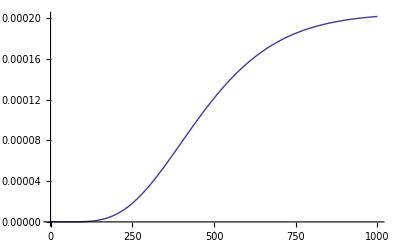

```mathematica
Plot[MYunrelanswer331/.subs,{t,0,1000}]
```

Note the asymptote is

```mathematica
probsProd331/.subs
```

0.0002048

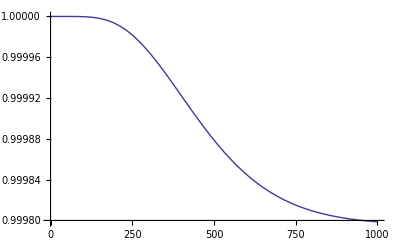

```mathematica
Plot[MYrelanswer331/.subs,{t,0,1000}]
```

### More comparisons between the ME computation and “exponomial” formula

#### m=2 case, distinct μ's

```mathematica
MyF22=Collect[MYFormulaUnrel[1,{μ1,μ2},{p1,p2},t],{ⅇ^(-t μ1),ⅇ^(-t μ2)},Simplify]
```

p1 p2-(ⅇ^(-t μ2) p1 p2 μ1)/(μ1-μ2)+(ⅇ^(-t μ1) p1 p2 μ2)/(μ1-μ2)

```mathematica
MYFormulaUnrel[1,{μ1,μ2},{p1,p2},t]
```

p1 p2-(ⅇ^(-t μ2) p1 p2 μ1)/(μ1-μ2)+(ⅇ^(-t μ1) p1 p2 μ2)/(μ1-μ2)

In the simple case where the transition probabilities are 1, we get the hypoexponential distribution (see computation and comment following this one)

```mathematica
MyF22sub=Expand[(MyF22/.{p1->λ1/μ1,p2->λ2/μ2})]
```

(ⅇ^(-t μ1) λ1 λ2)/(μ1 (μ1-μ2))+(λ1 λ2)/(μ1 μ2)-(ⅇ^(-t μ2) λ1 λ2)/((μ1-μ2) μ2)

```mathematica
MYFormulaUnrel[1,{μ1,μ2},{λ1/μ1,λ2/μ2},t]
```

(λ1 λ2)/(μ1 μ2)-(ⅇ^(-t μ2) λ1 λ2)/((μ1-μ2) μ2)+(ⅇ^(-t μ1) λ1 λ2)/(μ1^2-μ1 μ2)

Notice the derivative is the hypoexponential PDF as illustrated in Thm 3.3 on p. 174 of Orange Trivedi.

```mathematica
Collect[D[MyF22sub,t],{ⅇ^(-t μ1),ⅇ^(-t μ2)},Simplify]
```

-(ⅇ^(-t μ1) λ1 λ2)/(μ1-μ2)+(ⅇ^(-t μ2) λ1 λ2)/(μ1-μ2)

```mathematica
MYFormulaUnrel[1,{μ1,μ2},{λ1/μ1,λ2/μ2},t]
```

(λ1 λ2)/(μ1 μ2)-(ⅇ^(-t μ2) λ1 λ2)/((μ1-μ2) μ2)+(ⅇ^(-t μ1) λ1 λ2)/(μ1^2-μ1 μ2)

#### m=2 case, repeated μ's

```mathematica
MyF22R=Collect[MYFormulaUnrel[1,{μ1,μ1},{p1,p2},t],{ⅇ^(-t μ1),ⅇ^(-t μ2)},Simplify]
```

p1 p2-ⅇ^(-t μ1) p1 p2 (1+t μ1)

```mathematica
MYFormulaUnrel[1,{μ1,μ1},{p1,p2},t]
```

p1 p2-ⅇ^(-t μ1) p1 p2 (1+t μ1)

In the simple case where the transition probabilities are 1, we get the hypoexponential distribution (see computation and comment following this one)

```mathematica
MyF22Rsub=Expand[(MyF22R/.{p1->λ1/μ1,p2->λ1/μ1})]
```

λ1^2/μ1^2-(ⅇ^(-t μ1) λ1^2)/μ1^2-(ⅇ^(-t μ1) t λ1^2)/μ1

```mathematica
MYFormulaUnrel[1,{μ1,μ1},{λ1/μ1,λ1/μ1},t]
```

λ1^2/μ1^2-(ⅇ^(-t μ1) λ1^2 (1+t μ1))/μ1^2

We can recover my formula for the 2-dimensional distinct μ case using the acyclic ME representation, as follows.

```mathematica
m2mat={{μ1,0,0},{0,μ2,0},{0,0,0}};
p2mat={{0,p12,0},{0,0,p23},{0,0,1}};
MEF22=Collect[MEFormulaUnrelAcyclic[m2mat,p2mat,3,t],{ⅇ^(-t μ1),ⅇ^(-t μ2)},Simplify]
```

p12 p23-(ⅇ^(-t μ2) p12 p23 μ1)/(μ1-μ2)+(ⅇ^(-t μ1) p12 p23 μ2)/(μ1-μ2)

```mathematica
MEFormulaUnrelAcyclic[{{μ1,0,0},{0,μ2,0},{0,0,0}},{{0,p12,0},{0,0,p23},{0,0,1}},3,t]
```

(ⅇ^(-t μ1-t μ2) p12 p23 (-ⅇ^(t μ1) μ1+ⅇ^(t μ1+t μ2) μ1+ⅇ^(t μ2) μ2-ⅇ^(t μ1+t μ2) μ2))/(μ1-μ2)

```mathematica
MEF22sub=Expand[(MEF22/.{p12->λ1/μ1,p23->λ2/μ2})]
```

(ⅇ^(-t μ1) λ1 λ2)/(μ1 (μ1-μ2))+(λ1 λ2)/(μ1 μ2)-(ⅇ^(-t μ2) λ1 λ2)/((μ1-μ2) μ2)

```mathematica
MEFormulaUnrelAcyclic[{{μ1,0,0},{0,μ2,0},{0,0,0}},{{0,λ1/μ1,0},{0,0,λ2/μ2},{0,0,1}},3,t]
```

(ⅇ^(-t μ1-t μ2) λ1 λ2 (-ⅇ^(t μ1) μ1+ⅇ^(t μ1+t μ2) μ1+ⅇ^(t μ2) μ2-ⅇ^(t μ1+t μ2) μ2))/(μ1 (μ1-μ2) μ2)

### m=3 comparisions: repeated and distinct μ cases

#### m=3 case, repeated μ's.

“Exponomial” formula:

```mathematica
MyF33=Collect[MYFormulaUnrel[1,{μ1,μ1,μ1},{p1,p2,p3},t],{ⅇ^(-t μ1)},Simplify]
```

p1 p2 p3-1/2 ⅇ^(-t μ1) p1 p2 p3 (2+2 t μ1+t^2 μ1^2)

```mathematica
MYFormulaUnrel[1,{μ1,μ1,μ1},{p1,p2,p3},t]
```

p1 p2 p3-1/2 ⅇ^(-t μ1) p1 p2 p3 (2+2 t μ1+t^2 μ1^2)

```mathematica
MyF33sub=Expand[(MyF33/.{p1->λ1/μ1,p2->λ1/μ1,p3->λ1/μ1})]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

```mathematica
Expand[MYFormulaUnrel[1,{μ1,μ1,μ1},{λ1/μ1,λ1/μ1,λ1/μ1},t]]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

ME representation for repeated μ's case.

```mathematica
m3mat={{μ1,0,0,0},{0,μ1,0,0},{0,0,μ1,0},{0,0,0,0}};
p3mat={{0,p12,0,0},{0,0,p23,0},{0,0,0,p34},{0,0,0,1}};
MEF33=Collect[MEFormulaUnrelAcyclic[m3mat,p3mat,4,t],{ⅇ^(-t μ1)},Simplify]
```

p12 p23 p34-1/2 ⅇ^(-t μ1) p12 p23 p34 (2+2 t μ1+t^2 μ1^2)

```mathematica
MEFormulaUnrelAcyclic[{{μ1,0,0,0},{0,μ1,0,0},{0,0,μ1,0},{0,0,0,0}},{{0,p12,0,0},{0,0,p23,0},{0,0,0,p34},{0,0,0,1}},4,t]
```

1/2 ⅇ^(-t μ1) p12 p23 p34 (-2+2 ⅇ^(t μ1)-2 t μ1-t^2 μ1^2)

```mathematica
MEF33sub=Expand[(MEF33/.{p12->λ1/μ1,p23->λ1/μ1,p34->λ1/μ1})]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

```mathematica
Expand[MEFormulaUnrelAcyclic[{{μ1,0,0,0},{0,μ1,0,0},{0,0,μ1,0},{0,0,0,0}},{{0,λ1/μ1,0,0},{0,0,λ1/μ1,0},{0,0,0,λ1/μ1},{0,0,0,1}},4,t]]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

Now let's try distinct μ's.

“Exponomial” formula:

```mathematica
MyF111=Collect[MYFormulaUnrel[1,{μ1,μ2,μ3},{p12,p23,p34},t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]
```

p12 p23 p34-(ⅇ^(-t μ1) p12 p23 p34 μ2 μ3)/((μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) p12 p23 p34 μ1 μ3)/((μ1-μ2) (μ2-μ3))+(ⅇ^(-t μ3) p12 p23 p34 μ1 μ2)/((μ1-μ3) (-μ2+μ3))

```mathematica
MYFormulaUnrel[1,{μ1,μ2,μ3},{p12,p23,p34},t]
```

p12 p23 p34-(ⅇ^(-t μ1) p12 p23 p34 μ2 μ3)/((μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) p12 p23 p34 μ1 μ3)/((μ1-μ2) (μ2-μ3))+(ⅇ^(-t μ3) p12 p23 p34 μ1 μ2)/((μ1-μ3) (-μ2+μ3))

```mathematica
MyF111sub=Expand[(MyF111/.{p12->λ1/μ1,p23->λ2/μ2,p34->λ3/μ3})]
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

```mathematica
MYFormulaUnrel[1,{μ1,μ2,μ3},{λ1/μ1,λ2/μ2,λ3/μ3},t]
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

The ME approach.

```mathematica
m3mat111=DiagonalMatrix[{μ1,μ2,μ3,0}];
p3mat111={{0,p12,0,0},{0,0,p23,0},{0,0,0,p34},{0,0,0,1}};
Collect[MEFormulaUnrelAcyclic[m3mat111,p3mat111,4,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Simplify]/.{p12->λ1/μ1,p23->λ2/μ2,p34->λ3/μ3}
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

```mathematica
MEFormulaUnrelAcyclic[{{μ1,0,0,0},{0,μ2,0,0},{0,0,μ3,0},{0,0,0,0}},{{0,λ1/μ1,0,0},{0,0,λ2/μ2,0},{0,0,0,λ3/μ3},{0,0,0,1}},4,t]
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ2-μ3) μ3 (-μ1+μ3))

## Acyclic Markov chains with absorbing state using the ME approach

### The two ways we have found to reproduce the answers from “exponomial” formula for acyclic Markov chains with the ME formulation.

#### First way: simple but "non-intuitive" or if you prefer, "non-physical: simply multiply the "open" ME formulation by the product of the transition probabilies. For example:

```mathematica
ratelist33={μ1,μ1,μ1};
problist33={p12,p23,p34};
collectterms33={ⅇ^(-t μ1)};
```

#### “Exponomial” formula for the m=3 repeated μ's case

```mathematica
MyF33=Collect[MYFormulaUnrel[1,ratelist33,problist33,t],collectterms33,Simplify]
```

p12 p23 p34-1/2 ⅇ^(-t μ1) p12 p23 p34 (2+2 t μ1+t^2 μ1^2)

Substitute λ/μ ratios for transition probabilities.

```mathematica
MyF33sub=Expand[(MyF33/.{p12->λ1/μ1,p23->λ1/μ1,p34->λ1/μ1})]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

enter λ/μ ratios for transition probabilities directly.

```mathematica
Expand[MYFormulaUnrel[1,ratelist33,{λ1/μ1,λ1/μ1,λ1/μ1},t]]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

#### ME representation for m=3 repeated μ's case, the simple but less "physical" way

Gives right answer, but requires the rather arbitrary pre-multiplication by the produact of the transition probs.

```mathematica
mMat33simple=DiagonalMatrix[{μ1,μ1,μ1}];
pMat33simple={{0,1,0},{0,0,1},{0,0,0}};
MEF33simple=Collect[p12 p23 p34 MEFormulaUnrel[mMat33simple,pMat33simple,3,t],collectterms33,Simplify]
```

p12 p23 p34-1/2 ⅇ^(-t μ1) p12 p23 p34 (2+2 t μ1+t^2 μ1^2)

```mathematica
MEF33subsimple=Expand[(MEF33simple/.{p12->λ1/μ1,p23->λ1/μ1,p34->λ1/μ1})]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

#### ME representation for m=3 repeated μ's case, the more complicated but more "physical" way

More intuitive, in that the transition probs appear naturally in the P matrix, but requires increasing the dimension of the representation from 3 to 4.

```mathematica
mMat33augmented={{μ1,0,0,0},{0,μ1,0,0},{0,0,μ1,0},{0,0,0,0}};
pMat33augmented={{0,p12,0,0},{0,0,p23,0},{0,0,0,p34},{0,0,0,1}};
MEF33augmented=Collect[MEFormulaUnrelAcyclic[mMat33augmented,pMat33augmented,4,t],collectterms33,Simplify]
```

p12 p23 p34-1/2 ⅇ^(-t μ1) p12 p23 p34 (2+2 t μ1+t^2 μ1^2)

```mathematica
MEF33subaugmented=Expand[(MEF33augmented/.{p12->λ1/μ1,p23->λ1/μ1,p34->λ1/μ1})]
```

λ1^3/μ1^3-(ⅇ^(-t μ1) λ1^3)/μ1^3-(ⅇ^(-t μ1) t λ1^3)/μ1^2-(ⅇ^(-t μ1) t^2 λ1^3)/(2 μ1)

## Acyclic Markov chain example from red Sahner, Trivedi, Puliafito, pp. 74-76

Note that this clarifies the fact that “exponomial” approach as currently formulated works only when the chain is acyclic, that is, once the process leaves a state, it never returns. Note also in this example, there are two absorbing states. In order to use my formula, we must decompose the chain into all possible paths to the two absorbing states. They are 1345, 135, 136, 2345, 235, and 236.

### Using “exponomial” formula -- sum over all paths

Define rates out of the states and the transition probabilities.

```mathematica
initprobs={π1->4/10,π2->4/10,π3->2/10};
rates={μ1->4,μ2->1,μ3->10,μ4->2};
trans={p13->1,p23->1,p34->2/10,p35->5/10,p36->3/10,p45->1};
mcAll=Union[initprobs,rates,trans];
```

```mathematica
fexp1345=MYFormulaUnrel[1,{μ1,μ3,μ4},{p13,p34,p45},t];
fexp135=MYFormulaUnrel[1,{μ1,μ3},{p13,p35},t];
fexp136=MYFormulaUnrel[1,{μ1,μ3},{p13,p36},t];
fexp2345=MYFormulaUnrel[1,{μ2,μ3,μ4},{p23,p34,p45},t];
fexp235=MYFormulaUnrel[1,{μ2,μ3},{p23,p35},t];
fexp236=MYFormulaUnrel[1,{μ2,μ3},{p23,p36},t];
fexp345=MYFormulaUnrel[1,{μ3,μ4},{p34,p45},t];
fexp35=MYFormulaUnrel[1,{μ3},{p35},t];
fexp36=MYFormulaUnrel[1,{μ3},{p36},t];
```

Individual path probabilities distributions (without initial probs)

```mathematica
Column[Collect[{π1*fexp1345,
π1*fexp135,
π1*fexp136,
π2*fexp2345,
π2*fexp235,
π2*fexp236,
π3*fexp345,
π3*fexp35,
π3*fexp36}/.mcAll,{ⅇ^(-10 t),ⅇ^(-4 t),ⅇ^(-2 t),ⅇ^-t},Simplify]]
```

2/25-ⅇ^(-10 t)/75+(2 ⅇ^(-4 t))/15-ⅇ^(-2 t)/5
1/5+(2 ⅇ^(-10 t))/15-ⅇ^(-4 t)/3
3/25+(2 ⅇ^(-10 t))/25-ⅇ^(-4 t)/5
2/25-ⅇ^(-10 t)/450+ⅇ^(-2 t)/10-(8 ⅇ^-t)/45
1/5+ⅇ^(-10 t)/45-(2 ⅇ^-t)/9
3/25+ⅇ^(-10 t)/75-(2 ⅇ^-t)/15
1/25+ⅇ^(-10 t)/100-ⅇ^(-2 t)/20
1/10-ⅇ^(-10 t)/10
3/50-(3 ⅇ^(-10 t))/50

Overall waiting time distribution (including initial probs).

```mathematica
Collect[fexpAll=
(π1*(fexp1345+fexp135+fexp136)
+π2*(fexp2345+fexp235+fexp236)
+π3*(fexp345+fexp35+fexp36))/.mcAll,
{ⅇ^(- t),ⅇ^(-2 t),ⅇ^(-4 t),ⅇ^(-10t)},Simplify]
```

1+ⅇ^(-10 t)/12-(2 ⅇ^(-4 t))/5-(3 ⅇ^(-2 t))/20-(8 ⅇ^-t)/15

From Sahner, Trivedi, and Puliafito (p. 76)

```mathematica
eSTP=1-16/30 ⅇ^-t-3/20 ⅇ^(-2 t)-2/5 ⅇ^(-4t)+5/60 ⅇ^(-10 t)
```

1+ⅇ^(-10 t)/12-(2 ⅇ^(-4 t))/5-(3 ⅇ^(-2 t))/20-(8 ⅇ^-t)/15

YES!!!

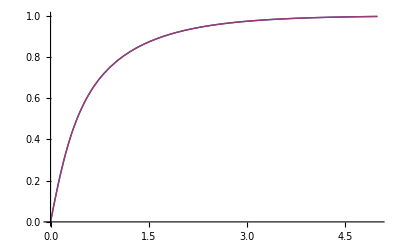

```mathematica
Plot[{fexpAll,eSTP},{t,0,5},AxesOrigin->{0,0}]
```

Plot individual path waiting times.

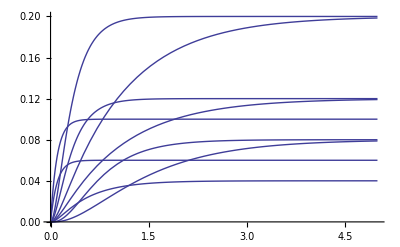

```mathematica
Plot[{π1*fexp1345,
π1*fexp135,
π1*fexp136,
π2*fexp2345,
π2*fexp235,
π2*fexp236,
π3*fexp345,
π3*fexp35,
π3*fexp36}/.mcAll,{t,0,5},AxesOrigin->{0,0}]
```

### ME formulation of Sahner, Trivedi, Pulafiato example

Define rates out of the states and the transition probabilities. Recall
initprobs = {π1 → 4/10, π2 → 4/10, π3 → 2/10};
rates = {μ1 → 4, μ2 → 1, μ3 → 10, μ4 → 2};
trans = {p13 → 1, p23 → 1, p34 → 2/10, p35 → 5/10, p36 → 3/10, p45 → 1};
mcAll = Union[initprobs, rates, trans];

To do this, we must add up the probabilities of being in states 5 or 6 at time t, given that the process started in either state 1, 2, or 3, weighted by 0.4, 0.4, 0.2, respectively.

```mathematica
pMatSTP={{0,0,p13,0,0,0},{0,0,p23,0,0,0},{0,0,0,p34,p35,p36},{0,0,0,0,p45,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
mMatSTP=DiagonalMatrix[{μ1,μ2,μ3,μ4,0,0}];
STPsubs={μ1->4,μ2->1,μ3->10,μ4->2,p13->1,p23->1,p34->2/10,p35->5/10,p36->3/10,p45->1};
pSTP={4/10,4/10,2/10,0,0,0};
ϵSTP={0,0,0,0,1,1};
expMatSTP=MatrixExp[-t mMatSTP.(IdentityMatrix[6]-pMatSTP)];
```

```mathematica
Collect[(pSTP. expMatSTP.ϵSTP)/.STPsubs,{ⅇ^(-10 t),ⅇ^(-4 t),ⅇ^(-2 t),ⅇ^-t},Simplify]
```

1+ⅇ^(-10 t)/12-(2 ⅇ^(-4 t))/5-(3 ⅇ^(-2 t))/20-(8 ⅇ^-t)/15

YES!! YES!! and YES!!

### The simplex, TMR, and TMR-simplex cases from Orange Trivedi pp. 160-161, p. 171, and pp. 175-176

#### Simplex first. One component -- system fails when component fails.

```mathematica
fsimplexMY=MYFormulaRel[1,{μ1},{1},t];
m1SimplexME={{μ1}};p1SimplexME={{0}};
fsimplexME=MEFormulaRel[m1SimplexME,p1SimplexME,1,t];
```

Compare my formula and ME versions.

```mathematica
{fsimplexMY,fsimplexME}
```

{ⅇ^(-t μ1),ⅇ^(-t μ1)}

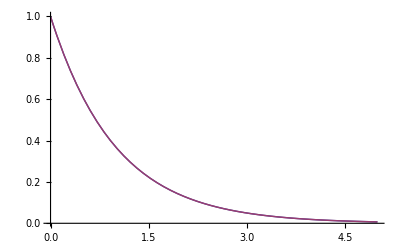

```mathematica
Plot[{fsimplexME/.{μ1->1},fsimplexMY/.{μ1->1}},{t,0,5},AxesOrigin->{0,0},PlotRange->All]
```

#### Triple-modular-redundant (TMR) next. Three components, 2-out-of-3 success, i.e., must have at least 2 components working or system fails.

```mathematica
fTMRMY=MYFormulaRel[1,{3μ1, 2μ1},{1,1},t];
m3TMRME={{3μ1,0},{0,2 μ1}};p3TMRME={{0,1},{0,0}};
fTMRME=MEFormulaRel[m3TMRME,p3TMRME,2,t];
```

Compare my formula and ME versions.

```mathematica
Column[Collect[{fTMRMY,fTMRME},{ⅇ^(- t μ1),ⅇ^(-2t μ1),ⅇ^(-3 t μ1)},Simplify]]
```

-2 ⅇ^(-3 t μ1)+3 ⅇ^(-2 t μ1)
-2 ⅇ^(-3 t μ1)+3 ⅇ^(-2 t μ1)

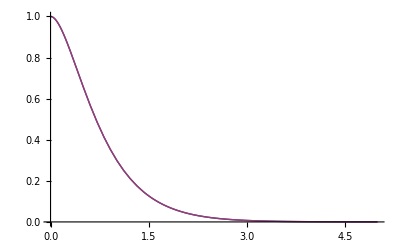

```mathematica
Plot[{fTMRMY/.{μ1->1},fTMRME/.{μ1->1}},{t,0,5},AxesOrigin->{0,0},PlotRange->All]
```

#### TMR-Simplex last. Like TMR, except, when first component fails, both failed component and one other (non-failed) component are discarded, leaving only one component. System fails when remaining single component fails.

```mathematica
fTMRsimplexMY=MYFormulaRel[1,{3 μ1,μ1},{1,1},t];
m3TMRsimplexME={{3μ1,0},{0, μ1}};p3TMRsimplexME={{0,1},{0,0}};
fTMRsimplexME=MEFormulaRel[m3TMRsimplexME,p3TMRsimplexME,2,t];
```

Compare “exponomil” formula and ME versions.

```mathematica
Simplify[Column[{fTMRsimplexMY,fTMRsimplexME}]]
```

1/2 ⅇ^(-3 t μ1) (-1+3 ⅇ^(2 t μ1))
1/2 ⅇ^(-3 t μ1) (-1+3 ⅇ^(2 t μ1))

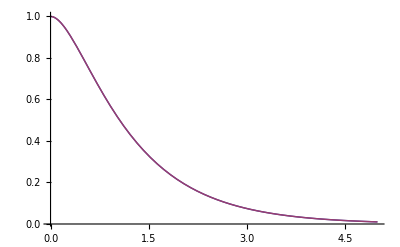

```mathematica
Plot[{fTMRsimplexMY/.{μ1->1},fTMRsimplexME/.{μ1->1}},{t,0,5},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Solve[(fTMRMY/.{μ1->1})==(fsimplexMY/.{μ1->1}),t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0},{t→Log[2]}}

```mathematica
Log[2.]
```

0.693147

#### Finally, compare simplex, TMR, and TMR-simplex. Notice that TMR-simplex is the most reliable for all t. TMR beats simplex only up to λ t=Log[2]~0.69, after which simplex is more reliable.

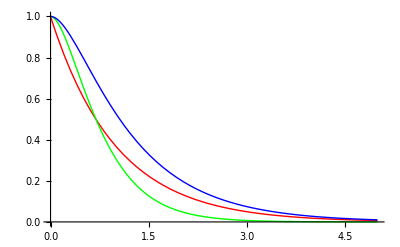

```mathematica
Plot[{fsimplexMY/.{μ1->1},fTMRMY/.{μ1->1},fTMRsimplexMY/.{μ1->1}},{t,0,5},AxesOrigin->{0,0},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

```mathematica
Plot[{fsimplexME/.{μ1->1},fTMRME/.{μ1->1},fTMRsimplexME/.{μ1->1}},{t,0,5},AxesOrigin->{0,0},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics-

## Reconciliation of infinite series symmetric-polynomial-based formula with Lipsky's Matrix Exponential formulation

### Matrix powers and symmetric functions

Define A=(γ1 | 1 | 0 | ... | 0
0 | γ2 | 1 | ... | 0
0 | 0 | γ3 | ... | 0
... | ... | ... | ... | 1
0 | 0 | 0 | 0 | γn) . Note that A^(j+n-1)[[1,n]]=𝒫_j(γ) for j=0, 1, 2,... and that A^k[[1,n]]=0 for k=0, 1, 2,...,n-2, that is, the first non-zero entry in the (1,n) position occurs in A^(n-1)and is equal to 1. 
Thus we can write the infinite series formula as P(t)=Λ∑_(j=0)^∞ (-1)^j 𝒫_j(γ)t^(n+j)/((n+j)!)=Λ∑_(j=0)^∞ (-1)^j A^(j+n-1)[[1,n]]t^(n+j)/((n+j)!)=Λ∑_(k=1)^∞ (-1)^(k+n)A^(k-1)[[1,n]]t^k/(k!), the last equality due to the fact that A^(k-1)[[1,n]]=0 for k=1, 2,...,n-1.

Thus P(t)=Λ (-1)^n(A^-1∑_(k=1)^∞ (-1)^k(A^k t^k)/(k!))[[1,n]]=(-1)^n Λ (A^-1 (ⅇ^(-t A)-I))[[1,n]]

### So how do we prove in general that 1-Ψ[exp(-t B)]=Λ t^m/(m!)∑_(j=0)^∞ (-1)^j 𝒫_j(μ)t^j/((m+j)_j) ? We initially assume p=(1,0,0,...,0). Will tackle the general case of initial state prob vector p later. Thus Ψ[exp(-t B)] is the sum of the elements of the first row in exp(-t B) .

Recall exp(-t B)=I-t B+1/(2!)(t B)^2-1/(3!)(t B)^3+....

### Consider the two different ways of calculating the reliability function

### Example with m=3, distinct μ's.

#### First use the augmented state method, i.e., add an absorbing state

One way is to augment the 3 states with an absorbing state, and compute the probability of being in the absorbing state at time t.

```mathematica
mMat3111augmented={{μ1,0,0,0},{0,μ2,0,0},{0,0,μ3,0},{0,0,0,0}};
pMat3111augmented={{0,p12,0,0},{0,0,p23,0},{0,0,0,p34},{0,0,0,1}};
collectterms3111={ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)};
MEF3111augmented=Collect[MEFormulaUnrelAcyclic[mMat3111augmented,pMat3111augmented,4,t],collectterms3111,Simplify];
subs3111augmented = {p12->λ1/μ1,p23->λ2/μ2,p34->λ3/μ3};
MEF3111subaugmented=Expand[(MEF3111augmented/.subs3111augmented)]
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

Let's look at the powers of B=M(I-P) .

```mathematica
bMat3111augmented = mMat3111augmented.(IdentityMatrix[4]-pMat3111augmented);
MatrixForm[bMat3111augmented]/.subs3111augmented
```

(μ1 | -λ1 | 0 | 0
0 | μ2 | -λ2 | 0
0 | 0 | μ3 | -λ3
0 | 0 | 0 | 0)

To clearly visualize the appearance of the complete symmetric functions, multiply by k!/(λ1 λ2 λ3 t^k) to leave only the terms involving μ1, μ2,μ3.

```mathematica
MatrixForm[Table[Expand[k!/(λ1 λ2 λ3 t^k)MatrixPower[-t bMat3111augmented,k][[1,4]]/k!],{k,1,10}]/.subs3111augmented]
```

(0
0
1
-μ1-μ2-μ3
μ1^2+μ1 μ2+μ2^2+μ1 μ3+μ2 μ3+μ3^2
-μ1^3-μ1^2 μ2-μ1 μ2^2-μ2^3-μ1^2 μ3-μ1 μ2 μ3-μ2^2 μ3-μ1 μ3^2-μ2 μ3^2-μ3^3
μ1^4+μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ2^4+μ1^3 μ3+μ1^2 μ2 μ3+μ1 μ2^2 μ3+μ2^3 μ3+μ1^2 μ3^2+μ1 μ2 μ3^2+μ2^2 μ3^2+μ1 μ3^3+μ2 μ3^3+μ3^4
-μ1^5-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4-μ2^5-μ1^4 μ3-μ1^3 μ2 μ3-μ1^2 μ2^2 μ3-μ1 μ2^3 μ3-μ2^4 μ3-μ1^3 μ3^2-μ1^2 μ2 μ3^2-μ1 μ2^2 μ3^2-μ2^3 μ3^2-μ1^2 μ3^3-μ1 μ2 μ3^3-μ2^2 μ3^3-μ1 μ3^4-μ2 μ3^4-μ3^5
μ1^6+μ1^5 μ2+μ1^4 μ2^2+μ1^3 μ2^3+μ1^2 μ2^4+μ1 μ2^5+μ2^6+μ1^5 μ3+μ1^4 μ2 μ3+μ1^3 μ2^2 μ3+μ1^2 μ2^3 μ3+μ1 μ2^4 μ3+μ2^5 μ3+μ1^4 μ3^2+μ1^3 μ2 μ3^2+μ1^2 μ2^2 μ3^2+μ1 μ2^3 μ3^2+μ2^4 μ3^2+μ1^3 μ3^3+μ1^2 μ2 μ3^3+μ1 μ2^2 μ3^3+μ2^3 μ3^3+μ1^2 μ3^4+μ1 μ2 μ3^4+μ2^2 μ3^4+μ1 μ3^5+μ2 μ3^5+μ3^6
-μ1^7-μ1^6 μ2-μ1^5 μ2^2-μ1^4 μ2^3-μ1^3 μ2^4-μ1^2 μ2^5-μ1 μ2^6-μ2^7-μ1^6 μ3-μ1^5 μ2 μ3-μ1^4 μ2^2 μ3-μ1^3 μ2^3 μ3-μ1^2 μ2^4 μ3-μ1 μ2^5 μ3-μ2^6 μ3-μ1^5 μ3^2-μ1^4 μ2 μ3^2-μ1^3 μ2^2 μ3^2-μ1^2 μ2^3 μ3^2-μ1 μ2^4 μ3^2-μ2^5 μ3^2-μ1^4 μ3^3-μ1^3 μ2 μ3^3-μ1^2 μ2^2 μ3^3-μ1 μ2^3 μ3^3-μ2^4 μ3^3-μ1^3 μ3^4-μ1^2 μ2 μ3^4-μ1 μ2^2 μ3^4-μ2^3 μ3^4-μ1^2 μ3^5-μ1 μ2 μ3^5-μ2^2 μ3^5-μ1 μ3^6-μ2 μ3^6-μ3^7)

```mathematica
Table[MatrixForm[Expand[MatrixPower[bMat3111augmented,k]]/.subs3111augmented],{k,1,5}]
```

{(μ1 | -λ1 | 0 | 0
0 | μ2 | -λ2 | 0
0 | 0 | μ3 | -λ3
0 | 0 | 0 | 0),(μ1^2 | -λ1 μ1-λ1 μ2 | λ1 λ2 | 0
0 | μ2^2 | -λ2 μ2-λ2 μ3 | λ2 λ3
0 | 0 | μ3^2 | -λ3 μ3
0 | 0 | 0 | 0),(μ1^3 | -λ1 μ1^2-λ1 μ1 μ2-λ1 μ2^2 | λ1 λ2 μ1+λ1 λ2 μ2+λ1 λ2 μ3 | -λ1 λ2 λ3
0 | μ2^3 | -λ2 μ2^2-λ2 μ2 μ3-λ2 μ3^2 | λ2 λ3 μ2+λ2 λ3 μ3
0 | 0 | μ3^3 | -λ3 μ3^2
0 | 0 | 0 | 0),(μ1^4 | -λ1 μ1^3-λ1 μ1^2 μ2-λ1 μ1 μ2^2-λ1 μ2^3 | λ1 λ2 μ1^2+λ1 λ2 μ1 μ2+λ1 λ2 μ2^2+λ1 λ2 μ1 μ3+λ1 λ2 μ2 μ3+λ1 λ2 μ3^2 | -λ1 λ2 λ3 μ1-λ1 λ2 λ3 μ2-λ1 λ2 λ3 μ3
0 | μ2^4 | -λ2 μ2^3-λ2 μ2^2 μ3-λ2 μ2 μ3^2-λ2 μ3^3 | λ2 λ3 μ2^2+λ2 λ3 μ2 μ3+λ2 λ3 μ3^2
0 | 0 | μ3^4 | -λ3 μ3^3
0 | 0 | 0 | 0),(μ1^5 | -λ1 μ1^4-λ1 μ1^3 μ2-λ1 μ1^2 μ2^2-λ1 μ1 μ2^3-λ1 μ2^4 | λ1 λ2 μ1^3+λ1 λ2 μ1^2 μ2+λ1 λ2 μ1 μ2^2+λ1 λ2 μ2^3+λ1 λ2 μ1^2 μ3+λ1 λ2 μ1 μ2 μ3+λ1 λ2 μ2^2 μ3+λ1 λ2 μ1 μ3^2+λ1 λ2 μ2 μ3^2+λ1 λ2 μ3^3 | -λ1 λ2 λ3 μ1^2-λ1 λ2 λ3 μ1 μ2-λ1 λ2 λ3 μ2^2-λ1 λ2 λ3 μ1 μ3-λ1 λ2 λ3 μ2 μ3-λ1 λ2 λ3 μ3^2
0 | μ2^5 | -λ2 μ2^4-λ2 μ2^3 μ3-λ2 μ2^2 μ3^2-λ2 μ2 μ3^3-λ2 μ3^4 | λ2 λ3 μ2^3+λ2 λ3 μ2^2 μ3+λ2 λ3 μ2 μ3^2+λ2 λ3 μ3^3
0 | 0 | μ3^5 | -λ3 μ3^4
0 | 0 | 0 | 0)}

```mathematica
MatrixForm[MatrixExp[bMat3111augmented/.subs3111augmented]]
```

(ⅇ^μ1 | -((ⅇ^μ1-ⅇ^μ2) λ1)/(μ1-μ2) | -(λ1 λ2 (ⅇ^μ2 μ1-ⅇ^μ3 μ1-ⅇ^μ1 μ2+ⅇ^μ3 μ2+ⅇ^μ1 μ3-ⅇ^μ2 μ3))/((μ1-μ2) (μ1-μ3) (μ2-μ3)) | -(λ1 λ2 λ3 (-μ1^2 μ2+ⅇ^μ3 μ1^2 μ2+μ1 μ2^2-ⅇ^μ3 μ1 μ2^2+μ1^2 μ3-ⅇ^μ2 μ1^2 μ3-μ2^2 μ3+ⅇ^μ1 μ2^2 μ3-μ1 μ3^2+ⅇ^μ2 μ1 μ3^2+μ2 μ3^2-ⅇ^μ1 μ2 μ3^2))/(μ1 (μ1-μ2) μ2 (μ1-μ3) (μ2-μ3) μ3)
0 | ⅇ^μ2 | -((ⅇ^μ2-ⅇ^μ3) λ2)/(μ2-μ3) | -(λ2 λ3 (-μ2+ⅇ^μ3 μ2+μ3-ⅇ^μ2 μ3))/(μ2 (μ2-μ3) μ3)
0 | 0 | ⅇ^μ3 | -((-1+ⅇ^μ3) λ3)/μ3
0 | 0 | 0 | 1)

```mathematica
Table[MatrixForm[Expand[MatrixPower[bMat3111augmented,k]]]/.{λ1->μ1,λ2->μ2,λ3->μ3,p12->1,p23->1,p34->1},{k,1,5}]
```

{(μ1 | -μ1 | 0 | 0
0 | μ2 | -μ2 | 0
0 | 0 | μ3 | -μ3
0 | 0 | 0 | 0),(μ1^2 | -μ1^2-μ1 μ2 | μ1 μ2 | 0
0 | μ2^2 | -μ2^2-μ2 μ3 | μ2 μ3
0 | 0 | μ3^2 | -μ3^2
0 | 0 | 0 | 0),(μ1^3 | -μ1^3-μ1^2 μ2-μ1 μ2^2 | μ1^2 μ2+μ1 μ2^2+μ1 μ2 μ3 | -μ1 μ2 μ3
0 | μ2^3 | -μ2^3-μ2^2 μ3-μ2 μ3^2 | μ2^2 μ3+μ2 μ3^2
0 | 0 | μ3^3 | -μ3^3
0 | 0 | 0 | 0),(μ1^4 | -μ1^4-μ1^3 μ2-μ1^2 μ2^2-μ1 μ2^3 | μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ1^2 μ2 μ3+μ1 μ2^2 μ3+μ1 μ2 μ3^2 | -μ1^2 μ2 μ3-μ1 μ2^2 μ3-μ1 μ2 μ3^2
0 | μ2^4 | -μ2^4-μ2^3 μ3-μ2^2 μ3^2-μ2 μ3^3 | μ2^3 μ3+μ2^2 μ3^2+μ2 μ3^3
0 | 0 | μ3^4 | -μ3^4
0 | 0 | 0 | 0),(μ1^5 | -μ1^5-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4 | μ1^4 μ2+μ1^3 μ2^2+μ1^2 μ2^3+μ1 μ2^4+μ1^3 μ2 μ3+μ1^2 μ2^2 μ3+μ1 μ2^3 μ3+μ1^2 μ2 μ3^2+μ1 μ2^2 μ3^2+μ1 μ2 μ3^3 | -μ1^3 μ2 μ3-μ1^2 μ2^2 μ3-μ1 μ2^3 μ3-μ1^2 μ2 μ3^2-μ1 μ2^2 μ3^2-μ1 μ2 μ3^3
0 | μ2^5 | -μ2^5-μ2^4 μ3-μ2^3 μ3^2-μ2^2 μ3^3-μ2 μ3^4 | μ2^4 μ3+μ2^3 μ3^2+μ2^2 μ3^3+μ2 μ3^4
0 | 0 | μ3^5 | -μ3^5
0 | 0 | 0 | 0)}

#### Second, use the “natural” formulation, but multiply the result by the product of the λ’s at the end

One way is to augment the 3 states with an absorbing state, and compute the probability of being in the absorbing state at time t.

```mathematica
mMat3111natural={{μ1,0,0},{0,μ2,0},{0,0,μ3}};
pMat3111natural={{0,1,0},{0,0,1},{0,0,0}};
collectterms3111={ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)};
MEF3111natural=Collect[MEFormulaUnrel[mMat3111natural,pMat3111natural,3,t],collectterms3111,Simplify];
```

```mathematica
Collect[(λ1 λ2 λ3)/(μ1 μ2 μ3)*MEF3111natural,collectterms3111,Simplify]
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

Compare to the augmented version computed previously. Same result.

```mathematica
MEF3111subaugmented
```

-(ⅇ^(-t μ1) λ1 λ2 λ3)/(μ1 (μ1-μ2) (μ1-μ3))+(ⅇ^(-t μ2) λ1 λ2 λ3)/((μ1-μ2) μ2 (μ2-μ3))+(λ1 λ2 λ3)/(μ1 μ2 μ3)+(ⅇ^(-t μ3) λ1 λ2 λ3)/((μ1-μ3) μ3 (-μ2+μ3))

Let's look at the powers of B=M(I-P) .

```mathematica
bMat3111natural = mMat3111natural.(IdentityMatrix[3]-pMat3111natural);
MatrixForm[bMat3111natural]
```

(μ1 | -μ1 | 0
0 | μ2 | -μ2
0 | 0 | μ3)

To clearly visualize the appearance of the complete symmetric functions, multiply by k!/( t^k) to leave only the terms involving μ1, μ2,μ3.

```mathematica
MatrixForm[Table[Expand[1/t^k MatrixPower[-t bMat3111natural,k][[1,3]]],{k,1,10}]]
```

(0
μ1 μ2
-μ1^2 μ2-μ1 μ2^2-μ1 μ2 μ3
μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ1^2 μ2 μ3+μ1 μ2^2 μ3+μ1 μ2 μ3^2
-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4-μ1^3 μ2 μ3-μ1^2 μ2^2 μ3-μ1 μ2^3 μ3-μ1^2 μ2 μ3^2-μ1 μ2^2 μ3^2-μ1 μ2 μ3^3
μ1^5 μ2+μ1^4 μ2^2+μ1^3 μ2^3+μ1^2 μ2^4+μ1 μ2^5+μ1^4 μ2 μ3+μ1^3 μ2^2 μ3+μ1^2 μ2^3 μ3+μ1 μ2^4 μ3+μ1^3 μ2 μ3^2+μ1^2 μ2^2 μ3^2+μ1 μ2^3 μ3^2+μ1^2 μ2 μ3^3+μ1 μ2^2 μ3^3+μ1 μ2 μ3^4
-μ1^6 μ2-μ1^5 μ2^2-μ1^4 μ2^3-μ1^3 μ2^4-μ1^2 μ2^5-μ1 μ2^6-μ1^5 μ2 μ3-μ1^4 μ2^2 μ3-μ1^3 μ2^3 μ3-μ1^2 μ2^4 μ3-μ1 μ2^5 μ3-μ1^4 μ2 μ3^2-μ1^3 μ2^2 μ3^2-μ1^2 μ2^3 μ3^2-μ1 μ2^4 μ3^2-μ1^3 μ2 μ3^3-μ1^2 μ2^2 μ3^3-μ1 μ2^3 μ3^3-μ1^2 μ2 μ3^4-μ1 μ2^2 μ3^4-μ1 μ2 μ3^5
μ1^7 μ2+μ1^6 μ2^2+μ1^5 μ2^3+μ1^4 μ2^4+μ1^3 μ2^5+μ1^2 μ2^6+μ1 μ2^7+μ1^6 μ2 μ3+μ1^5 μ2^2 μ3+μ1^4 μ2^3 μ3+μ1^3 μ2^4 μ3+μ1^2 μ2^5 μ3+μ1 μ2^6 μ3+μ1^5 μ2 μ3^2+μ1^4 μ2^2 μ3^2+μ1^3 μ2^3 μ3^2+μ1^2 μ2^4 μ3^2+μ1 μ2^5 μ3^2+μ1^4 μ2 μ3^3+μ1^3 μ2^2 μ3^3+μ1^2 μ2^3 μ3^3+μ1 μ2^4 μ3^3+μ1^3 μ2 μ3^4+μ1^2 μ2^2 μ3^4+μ1 μ2^3 μ3^4+μ1^2 μ2 μ3^5+μ1 μ2^2 μ3^5+μ1 μ2 μ3^6
-μ1^8 μ2-μ1^7 μ2^2-μ1^6 μ2^3-μ1^5 μ2^4-μ1^4 μ2^5-μ1^3 μ2^6-μ1^2 μ2^7-μ1 μ2^8-μ1^7 μ2 μ3-μ1^6 μ2^2 μ3-μ1^5 μ2^3 μ3-μ1^4 μ2^4 μ3-μ1^3 μ2^5 μ3-μ1^2 μ2^6 μ3-μ1 μ2^7 μ3-μ1^6 μ2 μ3^2-μ1^5 μ2^2 μ3^2-μ1^4 μ2^3 μ3^2-μ1^3 μ2^4 μ3^2-μ1^2 μ2^5 μ3^2-μ1 μ2^6 μ3^2-μ1^5 μ2 μ3^3-μ1^4 μ2^2 μ3^3-μ1^3 μ2^3 μ3^3-μ1^2 μ2^4 μ3^3-μ1 μ2^5 μ3^3-μ1^4 μ2 μ3^4-μ1^3 μ2^2 μ3^4-μ1^2 μ2^3 μ3^4-μ1 μ2^4 μ3^4-μ1^3 μ2 μ3^5-μ1^2 μ2^2 μ3^5-μ1 μ2^3 μ3^5-μ1^2 μ2 μ3^6-μ1 μ2^2 μ3^6-μ1 μ2 μ3^7
μ1^9 μ2+μ1^8 μ2^2+μ1^7 μ2^3+μ1^6 μ2^4+μ1^5 μ2^5+μ1^4 μ2^6+μ1^3 μ2^7+μ1^2 μ2^8+μ1 μ2^9+μ1^8 μ2 μ3+μ1^7 μ2^2 μ3+μ1^6 μ2^3 μ3+μ1^5 μ2^4 μ3+μ1^4 μ2^5 μ3+μ1^3 μ2^6 μ3+μ1^2 μ2^7 μ3+μ1 μ2^8 μ3+μ1^7 μ2 μ3^2+μ1^6 μ2^2 μ3^2+μ1^5 μ2^3 μ3^2+μ1^4 μ2^4 μ3^2+μ1^3 μ2^5 μ3^2+μ1^2 μ2^6 μ3^2+μ1 μ2^7 μ3^2+μ1^6 μ2 μ3^3+μ1^5 μ2^2 μ3^3+μ1^4 μ2^3 μ3^3+μ1^3 μ2^4 μ3^3+μ1^2 μ2^5 μ3^3+μ1 μ2^6 μ3^3+μ1^5 μ2 μ3^4+μ1^4 μ2^2 μ3^4+μ1^3 μ2^3 μ3^4+μ1^2 μ2^4 μ3^4+μ1 μ2^5 μ3^4+μ1^4 μ2 μ3^5+μ1^3 μ2^2 μ3^5+μ1^2 μ2^3 μ3^5+μ1 μ2^4 μ3^5+μ1^3 μ2 μ3^6+μ1^2 μ2^2 μ3^6+μ1 μ2^3 μ3^6+μ1^2 μ2 μ3^7+μ1 μ2^2 μ3^7+μ1 μ2 μ3^8)

```mathematica
Table[MatrixForm[Expand[MatrixPower[bMat3111natural,k]]],{k,1,5}]
```

{(μ1 | -μ1 | 0
0 | μ2 | -μ2
0 | 0 | μ3),(μ1^2 | -μ1^2-μ1 μ2 | μ1 μ2
0 | μ2^2 | -μ2^2-μ2 μ3
0 | 0 | μ3^2),(μ1^3 | -μ1^3-μ1^2 μ2-μ1 μ2^2 | μ1^2 μ2+μ1 μ2^2+μ1 μ2 μ3
0 | μ2^3 | -μ2^3-μ2^2 μ3-μ2 μ3^2
0 | 0 | μ3^3),(μ1^4 | -μ1^4-μ1^3 μ2-μ1^2 μ2^2-μ1 μ2^3 | μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ1^2 μ2 μ3+μ1 μ2^2 μ3+μ1 μ2 μ3^2
0 | μ2^4 | -μ2^4-μ2^3 μ3-μ2^2 μ3^2-μ2 μ3^3
0 | 0 | μ3^4),(μ1^5 | -μ1^5-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4 | μ1^4 μ2+μ1^3 μ2^2+μ1^2 μ2^3+μ1 μ2^4+μ1^3 μ2 μ3+μ1^2 μ2^2 μ3+μ1 μ2^3 μ3+μ1^2 μ2 μ3^2+μ1 μ2^2 μ3^2+μ1 μ2 μ3^3
0 | μ2^5 | -μ2^5-μ2^4 μ3-μ2^3 μ3^2-μ2^2 μ3^3-μ2 μ3^4
0 | 0 | μ3^5)}

```mathematica
MatrixForm[MatrixExp[bMat3111natural]]
```

(ⅇ^μ1 | -((ⅇ^μ1-ⅇ^μ2) μ1)/(μ1-μ2) | -(μ1 μ2 (ⅇ^μ2 μ1-ⅇ^μ3 μ1-ⅇ^μ1 μ2+ⅇ^μ3 μ2+ⅇ^μ1 μ3-ⅇ^μ2 μ3))/((μ1-μ2) (μ1-μ3) (μ2-μ3))
0 | ⅇ^μ2 | -((ⅇ^μ2-ⅇ^μ3) μ2)/(μ2-μ3)
0 | 0 | ⅇ^μ3)

```mathematica
Table[MatrixForm[Expand[MatrixPower[bMat3111natural,k]]],{k,1,5}]
```

{(μ1 | -μ1 | 0
0 | μ2 | -μ2
0 | 0 | μ3),(μ1^2 | -μ1^2-μ1 μ2 | μ1 μ2
0 | μ2^2 | -μ2^2-μ2 μ3
0 | 0 | μ3^2),(μ1^3 | -μ1^3-μ1^2 μ2-μ1 μ2^2 | μ1^2 μ2+μ1 μ2^2+μ1 μ2 μ3
0 | μ2^3 | -μ2^3-μ2^2 μ3-μ2 μ3^2
0 | 0 | μ3^3),(μ1^4 | -μ1^4-μ1^3 μ2-μ1^2 μ2^2-μ1 μ2^3 | μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ1^2 μ2 μ3+μ1 μ2^2 μ3+μ1 μ2 μ3^2
0 | μ2^4 | -μ2^4-μ2^3 μ3-μ2^2 μ3^2-μ2 μ3^3
0 | 0 | μ3^4),(μ1^5 | -μ1^5-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4 | μ1^4 μ2+μ1^3 μ2^2+μ1^2 μ2^3+μ1 μ2^4+μ1^3 μ2 μ3+μ1^2 μ2^2 μ3+μ1 μ2^3 μ3+μ1^2 μ2 μ3^2+μ1 μ2^2 μ3^2+μ1 μ2 μ3^3
0 | μ2^5 | -μ2^5-μ2^4 μ3-μ2^3 μ3^2-μ2^2 μ3^3-μ2 μ3^4
0 | 0 | μ3^5)}

#### Let's look at powers of the basic bi-diagonal matrices with the rates on the diagonal and 1's on the super-diagonal.

```mathematica
rateMat211={{μ1,1},{0,μ2}};
Table[MatrixForm[Expand[MatrixPower[rateMat211,k]]],{k,1,5}]
```

{(μ1 | 1
0 | μ2),(μ1^2 | μ1+μ2
0 | μ2^2),(μ1^3 | μ1^2+μ1 μ2+μ2^2
0 | μ2^3),(μ1^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3
0 | μ2^4),(μ1^5 | μ1^4+μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ2^4
0 | μ2^5)}

```mathematica
MatrixForm[MatrixExp[rateMat211]]
```

(ⅇ^μ1 | (ⅇ^μ1-ⅇ^μ2)/(μ1-μ2)
0 | ⅇ^μ2)

Distinct μ’s. dimension 2, with an extra added absorbing state (“physical” ME representation).

```mathematica
rateMat211augmented={{μ1,0,0},{0,μ2,0},{0,0,0}};
probMat211augmented={{0,1,0},{0,0,1},{0,0,1}};
bMat211augmented=rateMat211augmented.(IdentityMatrix[3]-probMat211augmented);
MatrixForm[bMat211augmented]
```

(μ1 | -μ1 | 0
0 | μ2 | -μ2
0 | 0 | 0)

```mathematica
Table[MatrixForm[Expand[MatrixPower[bMat211augmented,k]]],{k,1,5}]
```

{(μ1 | -μ1 | 0
0 | μ2 | -μ2
0 | 0 | 0),(μ1^2 | -μ1^2-μ1 μ2 | μ1 μ2
0 | μ2^2 | -μ2^2
0 | 0 | 0),(μ1^3 | -μ1^3-μ1^2 μ2-μ1 μ2^2 | μ1^2 μ2+μ1 μ2^2
0 | μ2^3 | -μ2^3
0 | 0 | 0),(μ1^4 | -μ1^4-μ1^3 μ2-μ1^2 μ2^2-μ1 μ2^3 | μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3
0 | μ2^4 | -μ2^4
0 | 0 | 0),(μ1^5 | -μ1^5-μ1^4 μ2-μ1^3 μ2^2-μ1^2 μ2^3-μ1 μ2^4 | μ1^4 μ2+μ1^3 μ2^2+μ1^2 μ2^3+μ1 μ2^4
0 | μ2^5 | -μ2^5
0 | 0 | 0)}

The matrix exponential -- term in upper right-hand corner should be the unreliability, i.e., the probability of being in the absorbing state at time t, given the process started in state 1 at time 0. Indeed this gives the right answer. So how come the terms in the upper right-hand corner of the powers of the B matrix above are not the complete symmetric functions?

They actually are, and I just don’t recognize it. Re-write the upper right-hand corner terms from the matrix infinite series exp(-t B)=I-t B+1/(2!)(t B)^2-1/(3!)(t B)^3+...as 0-0*t+1/2!*μ1μ2 t^2-1/3!*μ1μ2(μ1+μ2)t^3+1/4!*μ1μ2(μ1^2+μ1μ2+μ2^2)-...=μ1μ2∑_(j=0)^∞ (-1)^j 𝒫_j(μ1,μ2)t^(j+2)/((j+2)!) , which is the right formula, since in this case we have λ1=μ1 and λ2=μ2.

```mathematica
MatrixForm[MatrixExp[-t bMat211augmented]]
```

(ⅇ^(-t μ1) | -(ⅇ^(-t μ1-t μ2) (-ⅇ^(t μ1)+ⅇ^(t μ2)) μ1)/(μ1-μ2) | 1-(ⅇ^(-t μ2) μ1)/(μ1-μ2)+(ⅇ^(-t μ1) μ2)/(μ1-μ2)
0 | ⅇ^(-t μ2) | ⅇ^(-t μ2) (-1+ⅇ^(t μ2))
0 | 0 | 1)

Check this to make sure. OK.

```mathematica
MYFormulaUnrel[1,{μ1,μ2},{1,1},t]
```

1-(ⅇ^(-t μ2) μ1)/(μ1-μ2)+(ⅇ^(-t μ1) μ2)/(μ1-μ2)

Distinct μ’s, without the extra state (“non-physical” ME repesentation).

```mathematica
rateMat22={{μ1,1},{0,μ1}};
Table[MatrixForm[Expand[MatrixPower[rateMat22,k]]],{k,1,5}]
```

{(μ1 | 1
0 | μ1),(μ1^2 | 2 μ1
0 | μ1^2),(μ1^3 | 3 μ1^2
0 | μ1^3),(μ1^4 | 4 μ1^3
0 | μ1^4),(μ1^5 | 5 μ1^4
0 | μ1^5)}

```mathematica
MatrixForm[MatrixExp[rateMat22]]
```

(ⅇ^μ1 | ⅇ^μ1
0 | ⅇ^μ1)

```mathematica
rateMat3111={{μ1,1,0},{0,μ2,1},{0,0,μ3}};
Table[MatrixForm[Expand[MatrixPower[rateMat3111,k]]],{k,1,5}]
```

{(μ1 | 1 | 0
0 | μ2 | 1
0 | 0 | μ3),(μ1^2 | μ1+μ2 | 1
0 | μ2^2 | μ2+μ3
0 | 0 | μ3^2),(μ1^3 | μ1^2+μ1 μ2+μ2^2 | μ1+μ2+μ3
0 | μ2^3 | μ2^2+μ2 μ3+μ3^2
0 | 0 | μ3^3),(μ1^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3 | μ1^2+μ1 μ2+μ2^2+μ1 μ3+μ2 μ3+μ3^2
0 | μ2^4 | μ2^3+μ2^2 μ3+μ2 μ3^2+μ3^3
0 | 0 | μ3^4),(μ1^5 | μ1^4+μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ2^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3+μ1^2 μ3+μ1 μ2 μ3+μ2^2 μ3+μ1 μ3^2+μ2 μ3^2+μ3^3
0 | μ2^5 | μ2^4+μ2^3 μ3+μ2^2 μ3^2+μ2 μ3^3+μ3^4
0 | 0 | μ3^5)}

```mathematica
MatrixForm[Collect[MatrixExp[rateMat3111],{ⅇ^μ1,ⅇ^μ2,ⅇ^μ3},Simplify]]
```

(ⅇ^μ1 | ⅇ^μ1/(μ1-μ2)+ⅇ^μ2/(-μ1+μ2) | ⅇ^μ1/((μ1-μ2) (μ1-μ3))-ⅇ^μ2/((μ1-μ2) (μ2-μ3))+ⅇ^μ3/((μ1-μ3) (μ2-μ3))
0 | ⅇ^μ2 | ⅇ^μ2/(μ2-μ3)+ⅇ^μ3/(-μ2+μ3)
0 | 0 | ⅇ^μ3)

```mathematica
rateMat41111={{μ1,1,0,0},{0,μ2,1,0},{0,0,μ3,1},{0,0,0,μ4}};
Table[MatrixForm[Expand[MatrixPower[rateMat41111,k]]],{k,1,5}]
```

{(μ1 | 1 | 0 | 0
0 | μ2 | 1 | 0
0 | 0 | μ3 | 1
0 | 0 | 0 | μ4),(μ1^2 | μ1+μ2 | 1 | 0
0 | μ2^2 | μ2+μ3 | 1
0 | 0 | μ3^2 | μ3+μ4
0 | 0 | 0 | μ4^2),(μ1^3 | μ1^2+μ1 μ2+μ2^2 | μ1+μ2+μ3 | 1
0 | μ2^3 | μ2^2+μ2 μ3+μ3^2 | μ2+μ3+μ4
0 | 0 | μ3^3 | μ3^2+μ3 μ4+μ4^2
0 | 0 | 0 | μ4^3),(μ1^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3 | μ1^2+μ1 μ2+μ2^2+μ1 μ3+μ2 μ3+μ3^2 | μ1+μ2+μ3+μ4
0 | μ2^4 | μ2^3+μ2^2 μ3+μ2 μ3^2+μ3^3 | μ2^2+μ2 μ3+μ3^2+μ2 μ4+μ3 μ4+μ4^2
0 | 0 | μ3^4 | μ3^3+μ3^2 μ4+μ3 μ4^2+μ4^3
0 | 0 | 0 | μ4^4),(μ1^5 | μ1^4+μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ2^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3+μ1^2 μ3+μ1 μ2 μ3+μ2^2 μ3+μ1 μ3^2+μ2 μ3^2+μ3^3 | μ1^2+μ1 μ2+μ2^2+μ1 μ3+μ2 μ3+μ3^2+μ1 μ4+μ2 μ4+μ3 μ4+μ4^2
0 | μ2^5 | μ2^4+μ2^3 μ3+μ2^2 μ3^2+μ2 μ3^3+μ3^4 | μ2^3+μ2^2 μ3+μ2 μ3^2+μ3^3+μ2^2 μ4+μ2 μ3 μ4+μ3^2 μ4+μ2 μ4^2+μ3 μ4^2+μ4^3
0 | 0 | μ3^5 | μ3^4+μ3^3 μ4+μ3^2 μ4^2+μ3 μ4^3+μ4^4
0 | 0 | 0 | μ4^5)}

```mathematica
MatrixForm[Simplify[MatrixExp[rateMat41111]]]
```

(ⅇ^μ1 | (ⅇ^μ1-ⅇ^μ2)/(μ1-μ2) | (ⅇ^μ3 (μ1-μ2)+ⅇ^μ1 (μ2-μ3)+ⅇ^μ2 (-μ1+μ3))/((μ1-μ2) (μ1-μ3) (μ2-μ3)) | (ⅇ^μ4 (μ1-μ2) (μ1-μ3) (μ2-μ3)-ⅇ^μ3 (μ1-μ2) (μ1-μ4) (μ2-μ4)+ⅇ^μ2 (μ1-μ3) (μ1-μ4) (μ3-μ4)-ⅇ^μ1 (μ2-μ3) (μ2-μ4) (μ3-μ4))/((-μ1+μ2) (μ1-μ3) (μ2-μ3) (μ1-μ4) (μ2-μ4) (μ3-μ4))
0 | ⅇ^μ2 | (ⅇ^μ2-ⅇ^μ3)/(μ2-μ3) | (ⅇ^μ4 (μ2-μ3)+ⅇ^μ2 (μ3-μ4)+ⅇ^μ3 (-μ2+μ4))/((μ2-μ3) (μ2-μ4) (μ3-μ4))
0 | 0 | ⅇ^μ3 | (ⅇ^μ3-ⅇ^μ4)/(μ3-μ4)
0 | 0 | 0 | ⅇ^μ4)

```mathematica
rateMat422={{μ1,1,0,0},{0,μ1,1,0},{0,0,μ2,1},{0,0,0,μ2}};
Table[MatrixForm[Expand[MatrixPower[rateMat422,k]]],{k,1,5}]
```

{(μ1 | 1 | 0 | 0
0 | μ1 | 1 | 0
0 | 0 | μ2 | 1
0 | 0 | 0 | μ2),(μ1^2 | 2 μ1 | 1 | 0
0 | μ1^2 | μ1+μ2 | 1
0 | 0 | μ2^2 | 2 μ2
0 | 0 | 0 | μ2^2),(μ1^3 | 3 μ1^2 | 2 μ1+μ2 | 1
0 | μ1^3 | μ1^2+μ1 μ2+μ2^2 | μ1+2 μ2
0 | 0 | μ2^3 | 3 μ2^2
0 | 0 | 0 | μ2^3),(μ1^4 | 4 μ1^3 | 3 μ1^2+2 μ1 μ2+μ2^2 | 2 μ1+2 μ2
0 | μ1^4 | μ1^3+μ1^2 μ2+μ1 μ2^2+μ2^3 | μ1^2+2 μ1 μ2+3 μ2^2
0 | 0 | μ2^4 | 4 μ2^3
0 | 0 | 0 | μ2^4),(μ1^5 | 5 μ1^4 | 4 μ1^3+3 μ1^2 μ2+2 μ1 μ2^2+μ2^3 | 3 μ1^2+4 μ1 μ2+3 μ2^2
0 | μ1^5 | μ1^4+μ1^3 μ2+μ1^2 μ2^2+μ1 μ2^3+μ2^4 | μ1^3+2 μ1^2 μ2+3 μ1 μ2^2+4 μ2^3
0 | 0 | μ2^5 | 5 μ2^4
0 | 0 | 0 | μ2^5)}

```mathematica
MatrixForm[Simplify[MatrixExp[rateMat422]]]
```

(ⅇ^μ1 | ⅇ^μ1 | (ⅇ^μ2+ⅇ^μ1 (-1+μ1-μ2))/(μ1-μ2)^2 | (ⅇ^μ1 (-2+μ1-μ2)+ⅇ^μ2 (2+μ1-μ2))/(μ1-μ2)^3
0 | ⅇ^μ1 | (ⅇ^μ1-ⅇ^μ2)/(μ1-μ2) | (ⅇ^μ1+ⅇ^μ2 (-1-μ1+μ2))/(μ1-μ2)^2
0 | 0 | ⅇ^μ2 | ⅇ^μ2
0 | 0 | 0 | ⅇ^μ2)

```mathematica
rateMat44={{μ1,1,0,0},{0,μ1,1,0},{0,0,μ1,1},{0,0,0,μ1}};
Table[MatrixForm[Expand[MatrixPower[rateMat44,k]]],{k,1,5}]
```

{(μ1 | 1 | 0 | 0
0 | μ1 | 1 | 0
0 | 0 | μ1 | 1
0 | 0 | 0 | μ1),(μ1^2 | 2 μ1 | 1 | 0
0 | μ1^2 | 2 μ1 | 1
0 | 0 | μ1^2 | 2 μ1
0 | 0 | 0 | μ1^2),(μ1^3 | 3 μ1^2 | 3 μ1 | 1
0 | μ1^3 | 3 μ1^2 | 3 μ1
0 | 0 | μ1^3 | 3 μ1^2
0 | 0 | 0 | μ1^3),(μ1^4 | 4 μ1^3 | 6 μ1^2 | 4 μ1
0 | μ1^4 | 4 μ1^3 | 6 μ1^2
0 | 0 | μ1^4 | 4 μ1^3
0 | 0 | 0 | μ1^4),(μ1^5 | 5 μ1^4 | 10 μ1^3 | 10 μ1^2
0 | μ1^5 | 5 μ1^4 | 10 μ1^3
0 | 0 | μ1^5 | 5 μ1^4
0 | 0 | 0 | μ1^5)}

Notice that the repeated cases can be generated simply by direct substitution into the distinct cases.

```mathematica
MatrixForm[Simplify[MatrixExp[rateMat44]]]
```

(ⅇ^μ1 | ⅇ^μ1 | ⅇ^μ1/2 | ⅇ^μ1/6
0 | ⅇ^μ1 | ⅇ^μ1 | ⅇ^μ1/2
0 | 0 | ⅇ^μ1 | ⅇ^μ1
0 | 0 | 0 | ⅇ^μ1)

```mathematica
MatrixForm[Expand[MatrixPower[rateMat41111,5]]/.{μ2->μ1,μ3->μ1,μ4->μ1}]
```

(μ1^5 | 5 μ1^4 | 10 μ1^3 | 10 μ1^2
0 | μ1^5 | 5 μ1^4 | 10 μ1^3
0 | 0 | μ1^5 | 5 μ1^4
0 | 0 | 0 | μ1^5)

```mathematica
MatrixForm[Inverse[%]]
```

(1/μ1^5 | -5/μ1^6 | 15/μ1^7 | -35/μ1^8
0 | 1/μ1^5 | -5/μ1^6 | 15/μ1^7
0 | 0 | 1/μ1^5 | -5/μ1^6
0 | 0 | 0 | 1/μ1^5)

### How about an ME representation of a two-state cyclic Markov process?

Single component with failure rate λ and recovery rate μ.

```mathematica
m2cyclic={{λ,0},{0,μ}};
p2cyclic={{0,1},{1,0}};
b2cyclic=m2cyclic.(IdentityMatrix[2]-p2cyclic);
MatrixForm[b2cyclic]
```

(λ | -λ
-μ | μ)

```mathematica
MatrixForm[Simplify[expcyclic2=MatrixExp[-t b2cyclic]]]
```

((ⅇ^(-t (λ+μ)) λ+μ)/(λ+μ) | (λ-ⅇ^(-t (λ+μ)) λ)/(λ+μ)
(μ-ⅇ^(-t (λ+μ)) μ)/(λ+μ) | (λ+ⅇ^(-t (λ+μ)) μ)/(λ+μ))

Note that unreliability formula will NOT give the right answer, since the sum of the terms in the first row is simply the probability of being in state 1 or state 2, which is always 1. Therefore the "unreliability" in this case turns out to be 0, and the "reliability" turns out to be 1.

```mathematica
Simplify[MEFormulaUnrel[m2cyclic,p2cyclic,2,t]]
```

0

Reliability -- probability of being in state 2 before time t.

```mathematica
Simplify[MEFormulaRel[m2cyclic,p2cyclic,2,t]]
```

1

The (1,1) entry is the probability of being in state 1 at time t, given the process started in state 1.
The (1,2) entry is the probability of being in state 2 at time t, given the process started in state 1.
The (2,1) entry is the probability of being in state 1 at time t, given the process started in state 2.
The (2,2) entry is the probability of being in state 2 at time t, given the process started in state 2.

If we identify state 1 with "system" (or "component") is up and state 2 with "system" (or "component") is down, 
then the long-term (steady-state) availability and unavailability are given by (starting in state 1)

```mathematica
Assuming[λ>0&&μ>0,Limit[expcyclic2[[1,All]],t->∞]]
```

{μ/(λ+μ),λ/(λ+μ)}

or by (starting in state 2)

```mathematica
Assuming[λ>0&&μ>0,Limit[expcyclic2[[2,All]],t->∞]]
```

{μ/(λ+μ),λ/(λ+μ)}

The real unreliability, i.e., time to reach state 2 for the first time, having started in state 1, i.e., first passage time, is given by

```mathematica
expcyclic2[[1,2]]
```

-((-1+ⅇ^(t (-λ-μ))) λ)/(λ+μ)

### The Laplace transform approach and the associated ODE

#### Preamble on Laplace Transforms and differential equations

Recall that if we start with the linear ODE ∑_(i=0)^m a_i f^(i)(t)=ϕ(t) and take Laplace transforms we get ∑_(i=0)^m a_i ℒ{f^(i)(t)}=ℒ{ϕ(t)}, so ℒ{f(t)}=(ℒ{ϕ(t)} + ∑_(i=1)^m a_i∑_(j=1)^i s^(i-j)f^(j-1)(0))/(∑_(i=0)^m a_i s^i) (since ℒ{f^(n)}=s^n-∑_(i=1)^n s^(n-i)f^(i-1)(0) for all n). Of course the f^(k)(0) are the initial conditions.

Let's compute the RLT of b(t) using the equation3.2.14b on p. 103 of Lipksky: ℒ{b(t)}=(ℒ{ϕ(t)}+∑_(i=1)^m a_i∑_(j=1)^i s^(i-j)ℒ{f^(j-1)(0)})/(∑_(i=0)^m a_i s^i)=Ψ[(s I+V)^-1]=(q_2(s))/(q_1(s)).

```mathematica
Collect[MEFormulaUnrelAcyclic[m3mat,p3mat,4,t],{ⅇ^(-t μ1),ⅇ^(-t μ2),ⅇ^(-t μ3)},Expand]
```

p12 p23 p34+ⅇ^(-t μ1) (-p12 p23 p34-p12 p23 p34 t μ1-1/2 p12 p23 p34 t^2 μ1^2)

```mathematica
LaplaceTransform[1/2 ⅇ^(-t μ) (-2+2 ⅇ^(t μ)-2 t μ-t^2 μ^2),t,s]
```

1/2 (2/s-(2 μ^2)/(s+μ)^3-(2 μ)/(s+μ)^2-2/(s+μ))

```mathematica
Together[1/2 (2/s-(2 μ^2)/(s+μ)^3-(2 μ)/(s+μ)^2-2/(s+μ))]
```

μ^3/(s (s+μ)^3)

Clearly q_1(s)=(s(s+μ))^3 and q_2(s)=μ^3.

Compute b(t) by taking inverse Laplace transform.

```mathematica
InverseLaplaceTransform[μ^3/(s(s+μ)^3),s,t]
```

1/2 ⅇ^(-t μ) (-2+2 ⅇ^(t μ)-2 t μ-t^2 μ^2)

Then compute B(t) (DF) as the integral of b(t) (PDF).

Yes!!

#### Relation to the underlying differential equation

What diff eq does this correspond to? Claim it is b'''(t)+3μ b''(t)+3 μ^2 b'(t)+μ^3 b(t)=0 (i.e., ϕ(t)=0) with initial conditions b(0)=0,b'(0)=0,b''(0)=μ^3. Note b(t) is the PDF, not the CDF B(t) that we were working with above.

```mathematica
trnsfrm=LaplaceTransform[b'''[t]+3μ b''[t]+3 μ^2 b'[t]+μ^3 b[t]==0,t,s]/.{LaplaceTransform[b[t],t,s]->SuperStar[B]}
```

-s^2 b[0]+s^3 B^*+μ^3 B^*+3 μ^2 (-b[0]+s B^*)+3 μ (-s b[0]+s^2 B^*-b'[0])-s b'[0]-b''[0]==0

```mathematica
Solve[trnsfrm,SuperStar[B]]
```

{{B^*→(s^2 b[0]+3 s μ b[0]+3 μ^2 b[0]+s b'[0]+3 μ b'[0]+b''[0])/(s+μ)^3}}

Transform with appropriate initial conditions -- note that result matches Ψ[(s I+V)^-1]=s(q_2(s))/(q_1(s)) from above. Note the s appears because we are working with the derivative b(t) of B(t), not B(t) directly.

```mathematica
Solve[trnsfrm,SuperStar[B]]/.{b[0]->0,b'[0]->0,b''[0]->μ^3}
```

{{B^*→μ^3/(s+μ)^3}}

Check that the diff eq and initial conditions are as advertised:

```mathematica
ff[t_]:=1/2 ⅇ^(-t μ) t^2 μ^3;Simplify[ff'''[t]+3μ ff''[t]+3 μ^2 ff'[t]+μ^3 ff[t]]
```

0

```mathematica
{ff[0],ff'[0],ff''[0]}
```

{0,0,μ^3}

Does this work as a PDF?

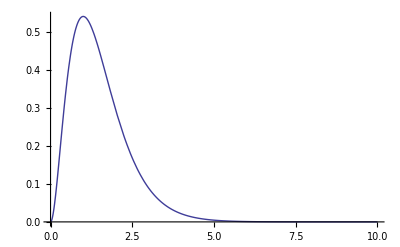

```mathematica
Plot[1/2 ⅇ^(-t μ) t^2 μ^3/.{μ->2},{t,0,10},PlotRange->All]
```

```mathematica
∫_0^∞ 1/2 ⅇ^(-t μ) t^2 μ^3 ⅆt/.{μ->2}
```

1

#### Agreement with the infinite sum version formula?

That is, does B(t)=∫_0^t 1/2 ⅇ^(-τ μ) τ^2 μ^3 ⅆτ=1-ⅇ^(-t μ)-ⅇ^(-t μ)t μ-1/2 ⅇ^(-t μ)t^2 μ^2=Λ ∑_(j=0)^∞ (-1)^j 𝒫_j(μ) t^(m+j)/((m+j)!)=μ^3 t^m/(m!)∑_(j=0)^∞ {j;m}(-μ t)^j/((m+j)_j)=μ^3 t^3/(3!)∑_(j=0)^∞ {j;3}(-μ t)^j/((3+j)_j),i.e., does 1-ⅇ^(-t μ)-ⅇ^(-t μ)t μ-1/2 ⅇ^(-t μ)t^2 μ^2=(μ t)^3/(3!)∑_(j=0)^∞ {j;3}(-μ t)^j/((3+j)_j) ?

```mathematica
Series[1- ⅇ^(-t μ) (1+t μ +1/2 t^2 μ^2),{t,0,10}]
```

(μ^3 t^3)/6-(μ^4 t^4)/8+(μ^5 t^5)/20-(μ^6 t^6)/72+(μ^7 t^7)/336-(μ^8 t^8)/1920+(μ^9 t^9)/12960-(μ^10 t^10)/100800+O[t]^11

Recall some definitions necessary to compute the infinite series terms.

```mathematica
symm3[x_,y_,z_,j_] := Sum[x^i y^l z^k, {i,0,j}, {l,0,j-i}, {k,j-i-l,j-i-l}];
term3[t_,j_] := (-1)^j/((3+j)!)  symm3[Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3],j] t^(3+j);
sum3[t_,k_] := Λ Sum[term3[t,j],{j,0,k}]
```

```mathematica
Expand[sum3[t,7]/.{Subscript[μ, 1]->μ,Subscript[μ, 2]->μ,Subscript[μ, 3]->μ,Λ->μ^3}]
```

(t^3 μ^3)/6-(t^4 μ^4)/8+(t^5 μ^5)/20-(t^6 μ^6)/72+(t^7 μ^7)/336-(t^8 μ^8)/1920+(t^9 μ^9)/12960-(t^10 μ^10)/100800

YES!!!

## Section head (*Section*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien.  (*Text*)

An inline formula: Fun[x_,y_]:=x+y (*Text and InlineFormula*)

An inline mathematical expression: x^2+7x+6=0 (*Text with inline math*)

```mathematica
Fun[x_,y_]:=x+y (*Code*)
```

### Subsection head (*Subsection*)

Pellentesque habitant morbi tristique senectus et netus et malesuada fames ac turpis egestas. Mauris scelerisque erat vel elit. Etiam a purus tincidunt tortor pulvinar laoreet. Proin tincidunt dolor ut lectus. Sed euismod augue http://www.wolfram.com. (*Text and Hyperlink*)

```mathematica
Fun[x_,y_]:=x+y (*InputOnly*)
```

Pellentesque habitant morbi tristique senectus et netus et malesuada fames ac turpis egestas. Mauris scelerisque erat vel elit. Etiam a purus tincidunt tortor pulvinar laoreet. Proin tincidunt dolor ut lectus. Sed euismod augue http://www.wolfram.com. (*Text and Hyperlink*)

```mathematica
Row[{Map[Sqrt, g[x^2, x^3]], "(*Output*)"}](*Input*)
```

g[√(x^2),√(x^3)](*Output*)

Vestibulum ornare, massa non auctor porta, erat elit varius lacus, a posuere nibh est ut pede. Fusce quis dolor. Pellentesque habitant morbi tristique senectus et netus et malesuada fames ac turpis egestas. Mauris scelerisque erat vel elit.  (*Text*)

Fun[x_, y_] := x + y (*Program*)

## Section head (*Section*)

### Subsection head (*Subsection*)

Pellentesque habitant morbi tristique senectus et netus et malesuada fames ac turpis egestas. Mauris scelerisque erat vel elit. Etiam a purus tincidunt tortor pulvinar laoreet. (*Text*)

ϕ_n(z)=1/(√(√π 2^n n!))e^(-z^2/2)H_n(z) (*DisplayFormula*)

#### Subsubsection head (*Subsubsection*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*Text*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*Item*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*ItemParagraph*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*Subitem*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*SubitemParagraph*)

## Section head (*Section*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. (*Text*)

```mathematica
Row[{Plot3D[Sin[x y],{x,0,4},{y,0,4},ImageSize->{400}],"(*Output*)"}] (*Input*)
```

-Graphics3D-(*Output*)

Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*Text*)

ϕ_n(z)=1/(√(√π 2^n n!))e^(-z^2/2)H_n(z) (*DisplayFormulaNumbered*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*ItemNumbered*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*ItemParagraph*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*SubitemNumbered*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. Mauris auctor nunc ac nisl. Nunc non turpis a dolor porta tristique. Nam accumsan massa scelerisque sapien. (*SubitemParagraph*)

```mathematica
Row[{Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}], "(*Output*)"}] (*Input*)
```

(*Output*)

## Section head (*Section*)

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Pellentesque enim dolor, euismod sit amet, rutrum nec, fermentum id, risus. (*Text*)

WolframAlphaQueryParseResults(*WolframAlphaShortInput*)

4

sum of 2 and 2 (*WolframAlphaLong*)